# spectrum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Level statistics\\QKT_nomemory.wl"];
```

```mathematica
LaunchKernels[12]
```

{Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12)}

## Method, k = 15

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

```mathematica
(*Floquet parameters*)
J=1000;
d=2 J+1;
α=0.84;
k=15.;
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.53835,0.53661}

```mathematica
phases=Sort[Arg[eigenvalm]];
(*2. Create a list of {phase,index} pairs*)
(*The index runs from 1 to the total number of eigenvalues*)
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

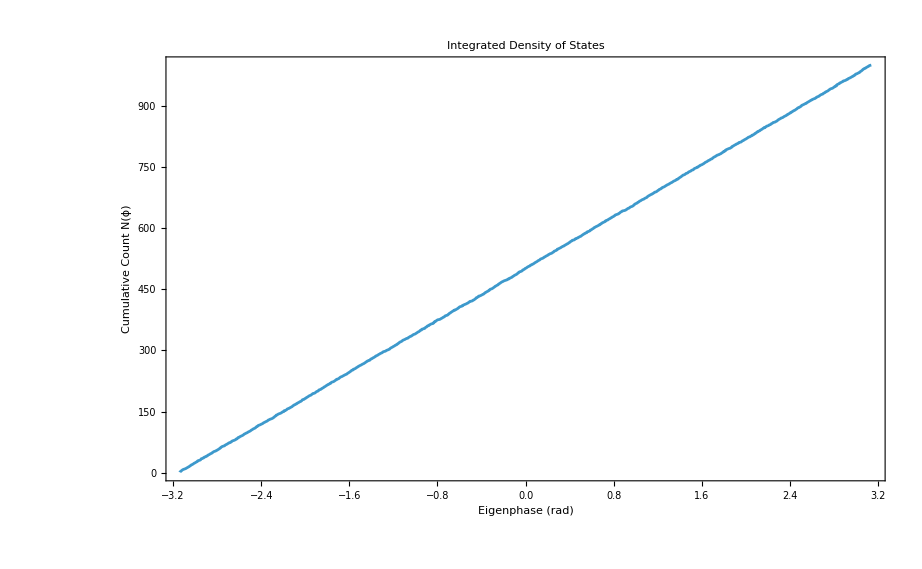

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

```mathematica
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

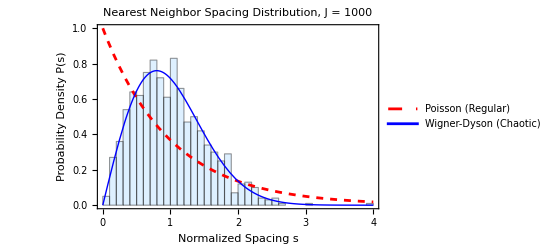

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

```mathematica
(*1. Create an efficient counting function using Interpolation*)(*This maps energy->index.n(E)*)
n=Length[unfolded];
staircase=Interpolation[Transpose[{unfolded,Range[n]}],InterpolationOrder->1];
```

```mathematica
(*2. Define the range of L and the spectrum boundaries*)
eMin=Min[unfolded];
eMax=Max[unfolded];
Lvalues=Range[0.5,20.0,0.25];
(*crucial:'unfolded' must be defined before running this*)
DistributeDefinitions[unfolded];
```

```mathematica
(*3. Parallel Calculation of Sigma^2(L)*)
sigmaData=ParallelTable[Module[{centers,counts,eMin,eMax},
eMin=Min[unfolded];
eMax=Max[unfolded];
(*Define centers for the sliding window*)(*Step size 0.2 gives good statistics without being too slow*)
centers=Range[eMin+L/2,eMax-L/2,0.2];
(*Count how many levels fall in each window*)
counts=Table[Count[unfolded,x_/;(c-L/2<=x<=c+L/2)],{c,centers}];
(*Return the pair {L,Variance}*)
{L,Variance[counts]}],{L,Lvalues},Method->"CoarsestGrained"];
```

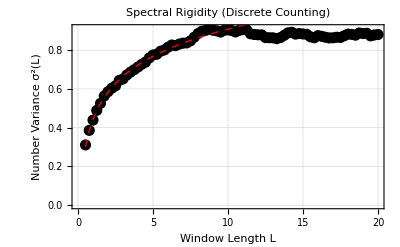

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,20,0.1}]]}]
```

```mathematica
(*4. Define Theoretical Curves*)
poisson[L_]:=L;
goe[L_]:=(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
gue[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
```

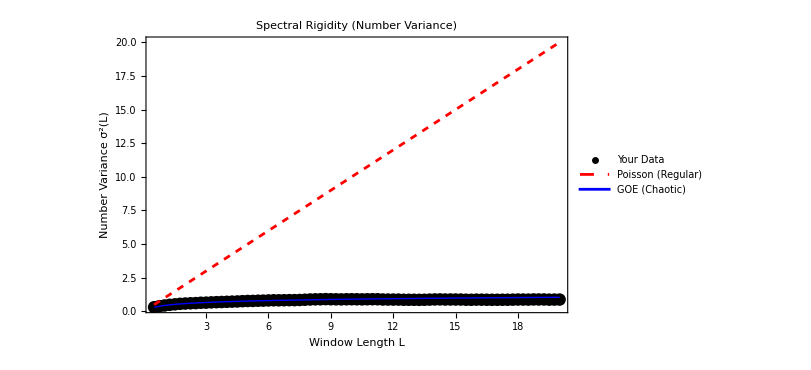

```mathematica
(*5. Plot*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{poisson[L],goe[L]},{L,0.5,20},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

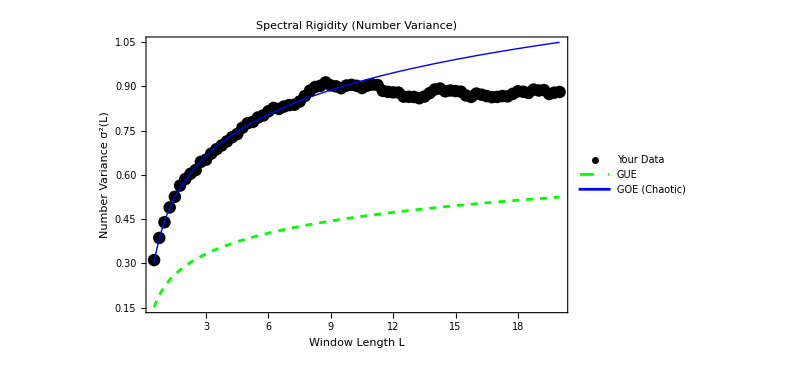

```mathematica
(*5. Plot*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{gue[L],goe[L]},{L,0.5,20},PlotStyle->{{Green,Dashed},{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

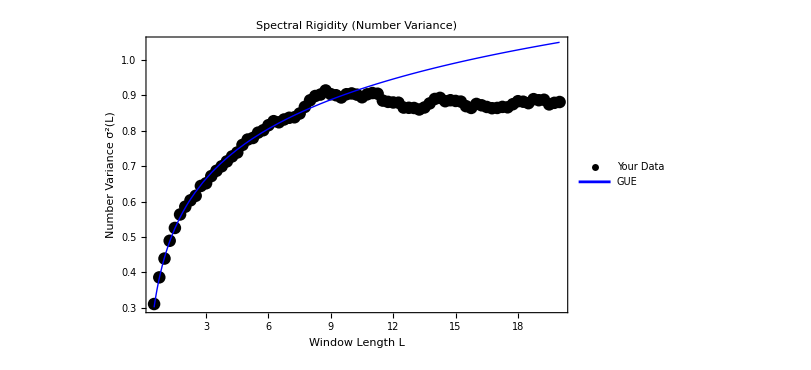

```mathematica
(*5. Plot*)
(*Positive parity*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{goe[L]},{L,0.5,20},PlotStyle->{{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

```mathematica
(*1. Define the Staircase Function*)(*Ensure'unfolded' is defined and sorted*)
nTotal=Length[unfolded];
staircaseFunc=Interpolation[Transpose[{unfolded,Range[nTotal]}],InterpolationOrder->1 ];
(*3. Parallel Calculation over L*)
LvaluesRigidity=Range[1,20,0.25]; (*Check L=1 to 20*)
```

```mathematica
(*1. Define Correct Discrete Delta3 Calculation*)(*This computes Delta3 directly from the eigenvalues in the window*)calcDelta3Discrete[center_,L_,spectrum_]:=Module[{inWindow,n,y,term1,term2},(*Find eigenvalues inside the window[center-L/2,center+L/2]*)inWindow=Select[spectrum,(center-L/2<=#<=center+L/2)&];
n=Length[inWindow];
(*If window is empty,deviation is just the linear fit of nothing (0)*)If[n==0,Return[0]];
(*Transform to relative coordinates[-L/2,L/2]*)y=inWindow-center;
(*We use the analytical formula for Delta3 of a step function.Ref:Bohigas,Giannoni,Schmit (1984)/Standard RMT texts.It relates to the moments of the positions in the window.*)(*This is a numerically stable integration of the step function deviation*)(*Delta3=(n^2)/16-(1/L^2)*Sum[y]^2+(3/L4)*Sum[y^2] is for the "stiffness" but direct integration of (N(x)-Ax-B)^2 is safer to implement:*)(*Let's stick to the definition:Min integral (N(x)-Ax-B)^2*)(*For a step function,this integral can be solved exactly.*)(*But to be safe and fast,let's use a high-res numeric integral of a Step Function*)(1/L)*NIntegrate[(Count[inWindow,v_/;v<=x]-(n/L)*(x-(center-L/2)))^2,{x,center-L/2,center+L/2},Method->"LocalAdaptive",AccuracyGoal->5]
(*Note:The term (n/L) above is an approximation of the average slope.For the exact Delta3,we subtract the BEST fit,not the average slope.*)];
(*FASTER METHOD:discrete summation moments*)
(*This formula is exact for Delta3 of a sequence of n levels x_i in[-L/2,L/2]*)
delta3Exact[L_,spectrum_]:=Module[{M1,M2,n},n=Length[spectrum];
If[n==0,Return[L/15]];(*Poisson empty limit approximation or 0*)(*Moments of the positions relative to window center*)M1=Total[spectrum];(*Sum x_i*)M2=Total[spectrum^2];(*Sum x_i^2*)(*Formula for min deviation of step function*)(*Delta3=n^2/12-n/L*M1+... this is getting complex to derive on the fly.*)(*Let's Use InterpolationOrder->0 (Step) which is reliable in Mathematica*)Nothing];
(*RE-RUN with InterpolationOrder->0*)
(*This is the easiest fix for your existing workflow*)
staircaseFuncStep=Interpolation[Transpose[{unfolded,Range[Length[unfolded]]}],InterpolationOrder->0 (*STRICT STEP FUNCTION*)];
calcDelta3WindowStep[center_,L_]:=Module[{min,max,meanN,slopeTerm,x},min=center-L/2;
max=center+L/2;
(*NIntegrate handles discontinuities automatically if limits are standard*)(*1. Average Height*)meanN=NIntegrate[staircaseFuncStep[x],{x,min,max}]/L;
(*2. Slope Term (Best Fit)*)slopeTerm=(12/L^3)*NIntegrate[(x-center)*(staircaseFuncStep[x]-meanN),{x,min,max}];
(*3. Compute Variance*)(1/L)*NIntegrate[(staircaseFuncStep[x]-(meanN+slopeTerm*(x-center)))^2,{x,min,max}]];
```

```mathematica
(*Calculate*)
delta3DataCorrected=ParallelTable[Module[{centers,d3Values,eMin,eMax},eMin=Min[unfolded]+L/2+0.5;
eMax=Max[unfolded]-L/2-0.5;
centers=Range[eMin,eMax,1.0];
d3Values=Map[calcDelta3WindowStep[#,L]&,centers];
{L,Mean[d3Values]}],{L,1,20,1},Method->"CoarsestGrained"];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$27$961197`x$9047 near {Notebook$$27$961197`x$9047} = {-481.76945040502802625789706534769801643025677437455478457906110634}. NIntegrate obtained -1.60237×10^-30 and 6.86277×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$27$961197`x$9445 near {Notebook$$27$961197`x$9445} = {-477.76945040502802625789706534769801643025677437455478457906110634}. NIntegrate obtained -1.60237×10^-30 and 6.86277×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$27$961197`x$11382 near {Notebook$$27$961197`x$11382} = {-457.76945040502802625789706534769801643025677437455478457906110634}. NIntegrate obtained -3.20475×10^-30 and 1.37255×10^-29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
(*Theoretical Predictions for Delta3(L) when L>>1*)(*EulerGamma is approx 0.577*)(*GOE:Time Reversal Symmetry (e.g.Standard QKT)*)
delta3GOE[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma-5/4-Pi^2/8);
(*GUE:Broken Time Reversal Symmetry*)
delta3GUE[L_]:=(1/(2*Pi^2))*(Log[2*Pi*L]+EulerGamma-5/4);
```

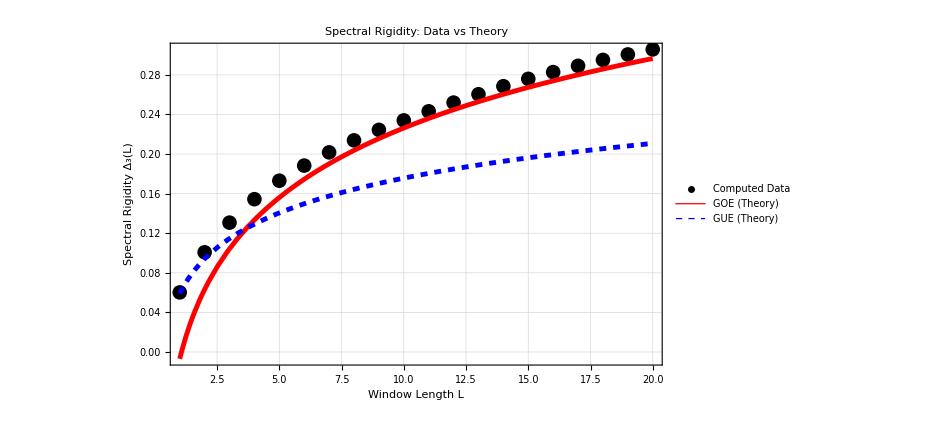

```mathematica
Show[(*Your Data*)ListPlot[delta3DataCorrected,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Computed Data"}],(*Theoretical Curves*)Plot[{delta3GOE[L],delta3GUE[L]},{L,1,20},PlotStyle->{{Red,Thickness[0.005]},{Blue,Dashed,Thickness[0.005]}},PlotLegends->{"GOE (Theory)","GUE (Theory)"}],Frame->True,FrameLabel->{"Window Length L","Spectral Rigidity \!\(\*SubscriptBox[\(Δ\), \(3\)]\)(L)"},PlotLabel->"Spectral Rigidity: Data vs Theory",GridLines->Automatic,ImageSize->700,PlotRange->All]
```

```mathematica
(*1. Define the Theoretical GOE Curve*)
Kgoe[tau_]:=If[tau<=1,2*tau-tau*Log[1+2*tau],2-tau*Log[(2*tau+1)/(2*tau-1)]];
(*2. Compute the "Raw" SFF from Unfolded Data*)
ComputeSFF[eigenvalues_,tauMax_,steps_]:=Module[{N,taus,Kraw},N=Length[eigenvalues];
taus=Range[0.01,tauMax,tauMax/steps];
(*Compute power spectrum for each time tau*)Kraw=Table[(1/N)*Abs[Sum[Exp[-I*2*Pi*e*t],{e,eigenvalues}]]^2,{t,taus}];
Transpose[{taus,Kraw}]];
(*3. CORRECTED SmoothSFF Function*)
SmoothSFF[data_,windowSize_]:=Module[{taus,kvals},taus=data[[All,1]];
kvals=data[[All,2]];
(*FIX:Apply MovingAverage to BOTH x and y to keep lengths equal and centered*)Transpose[{MovingAverage[taus,windowSize],MovingAverage[kvals,windowSize]}]];
```

```mathematica
(*---EXECUTION---*)
(*Parameters*)
tauLimit=2.0;
numPoints=2000;
smoothWindow=100; (*If the plot is still too noisy,increase this to 100*)
```

```mathematica
(*A.Calculate Raw SFF*)
sffRaw=ComputeSFF[unfolded,tauLimit,numPoints];
(*B.Smooth it*)
sffSmoothed=SmoothSFF[sffRaw,smoothWindow];
```

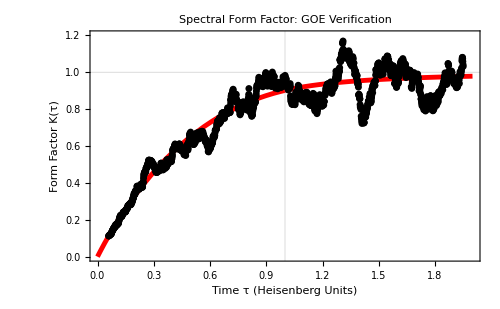

```mathematica
(*C.Plot Data vs GOE Theory*)
Show[(*Theoretical Curve (Red)*)Plot[Kgoe[tau],{tau,0,tauLimit},PlotStyle->{Red,Thickness[0.007]},PlotLabel->"Spectral Form Factor: GOE Verification"],(*Your Smoothed Data (Black)*)ListPlot[sffSmoothed,PlotStyle->{Black,PointSize[0.01]},Joined->False],Frame->True,FrameLabel->{"Time τ (Heisenberg Units)","Form Factor K(τ)"},GridLines->{{1},{1}},PlotRange->{{0,tauLimit},{0,1.2}},ImageSize->500]
```

```mathematica
(*3. Compute the Trace Power Spectrum*)
(*This is|Tr(U^t)|^2 which relates to Periodic Orbits*)
rawPhases=Arg[eigenvalM];
tMaxPO=100; (*Look at short times to see short orbits*)
powerSpectrum=Table[{t,Abs[Total[Exp[-I*t*rawPhases]]]^2},{t,1,tMaxPO}];
```

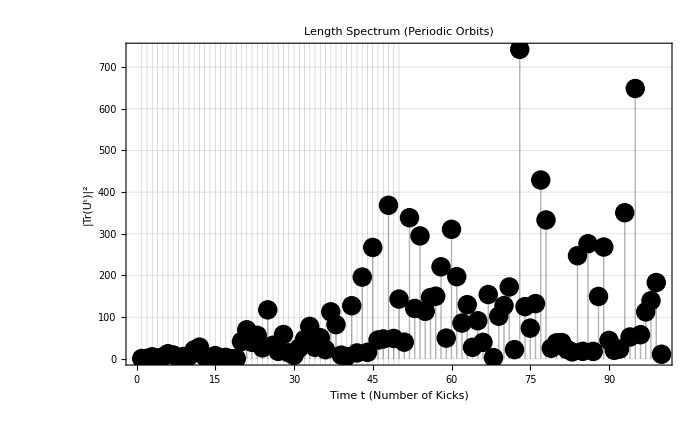

```mathematica
(*4. Plot*)
ListPlot[powerSpectrum,Filling->Axis,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Time t (Number of Kicks)","|Tr(\!\(\*SuperscriptBox[\(U\), \(t\)]\))|\!\(\*SuperscriptBox[\(\), \(2\)]\)"},PlotLabel->"Length Spectrum (Periodic Orbits)",GridLines->{Range[tMaxPO],Automatic},PlotRange->All,ImageSize->700]
```

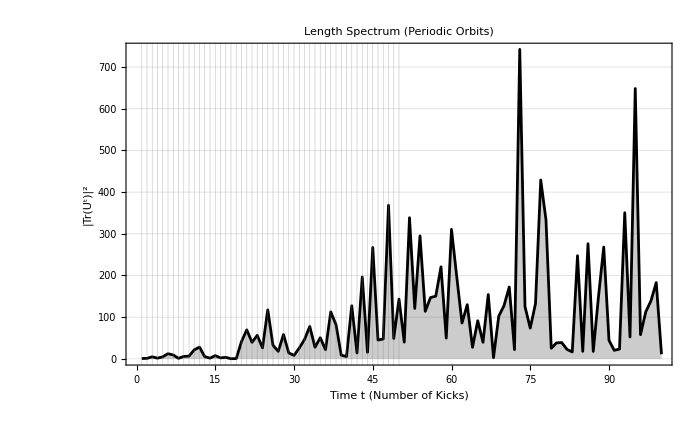

```mathematica
(*4. Plot*)
ListLinePlot[powerSpectrum,Filling->Axis,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Time t (Number of Kicks)","|Tr(\!\(\*SuperscriptBox[\(U\), \(t\)]\))|\!\(\*SuperscriptBox[\(\), \(2\)]\)"},PlotLabel->"Length Spectrum (Periodic Orbits)",GridLines->{Range[tMaxPO],Automatic},PlotRange->All,ImageSize->700]
```

```mathematica
dim=J+1;
(*1. Use the full time range up to system dimension*)
tMaxFull=10(J+1); (*This should be 1000*)
(*2. Compute Form Factor efficiently using Eigenvalues*)
(*We use the'rawPhases' list you created earlier.*)
(*This is much faster than MatrixPower*)
kDataFull=Table[Abs[Total[Exp[-I*t*rawPhases]]]^2,{t,1,tMaxFull}];
(*3. Reconstruction Formula (Summing all the way to N)*)
reconstructedSigmaFull[L_]:=(2/Pi^2)*Sum[(kDataFull[[t]]/t^2)*Sin[(Pi*L*t)/dim]^2,{t,1,tMaxFull}];
```

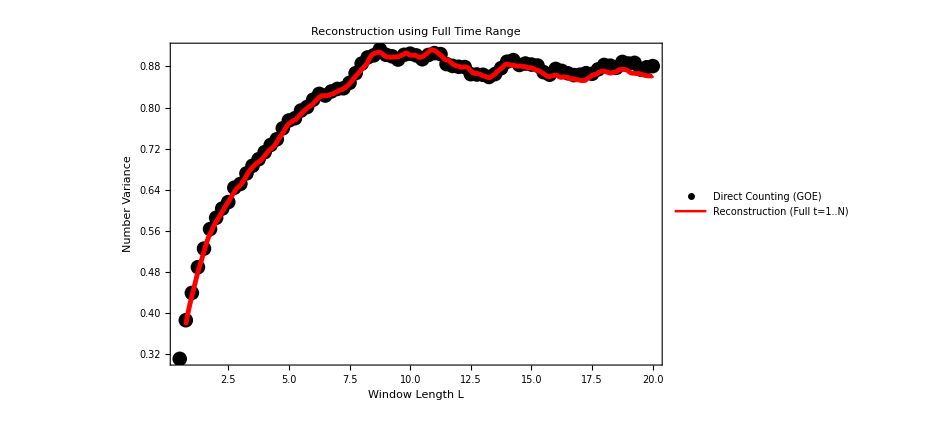

```mathematica
(*4. Plot Comparison*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Direct Counting (GOE)"}],Plot[reconstructedSigmaFull[L],{L,0,20},PlotStyle->{Red,Thickness[0.005]},PlotLegends->{"Reconstruction (Full t=1..N)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance"},PlotLabel->"Reconstruction using Full Time Range",PlotRange->All,ImageSize->700]
```

## Method, k = 30

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

```mathematica
(*Floquet parameters*)
J=500;
d=2 J+1;
α=0.84;
k=30.;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.535782,0.532225}

```mathematica
phases=Sort[Arg[eigenvalm]];
(*2. Create a list of {phase,index} pairs*)
(*The index runs from 1 to the total number of eigenvalues*)
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

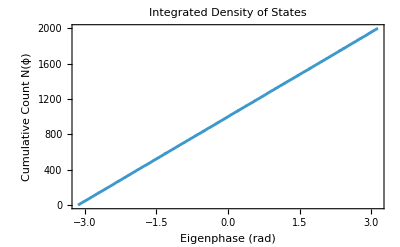

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

```mathematica
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

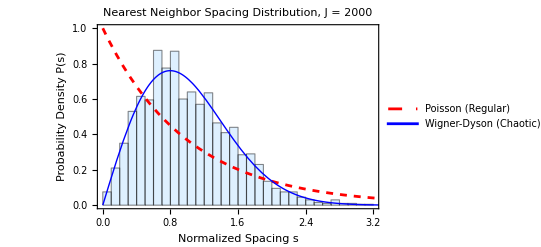

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

```mathematica
(*1. Create an efficient counting function using Interpolation*)(*This maps energy->index.n(E)*)
n=Length[unfolded];
staircase=Interpolation[Transpose[{unfolded,Range[n]}],InterpolationOrder->1];
```

```mathematica
(*2. Define the range of L and the spectrum boundaries*)
eMin=Min[unfolded];
eMax=Max[unfolded];
Lvalues=Range[0.5,100.0,0.2];
(*crucial:'unfolded' must be defined before running this*)
DistributeDefinitions[unfolded];
```

```mathematica
(*3. Parallel Calculation of Sigma^2(L)*)
sigmaData=ParallelTable[Module[{centers,counts,eMin,eMax},
eMin=Min[unfolded];
eMax=Max[unfolded];
(*Define centers for the sliding window*)(*Step size 0.2 gives good statistics without being too slow*)
centers=Range[eMin+L/2,eMax-L/2,0.2];
(*Count how many levels fall in each window*)
counts=Table[Count[unfolded,x_/;(c-L/2<=x<=c+L/2)],{c,centers}];
(*Return the pair {L,Variance}*)
{L,Variance[counts]}],{L,Lvalues},Method->"CoarsestGrained"];
```

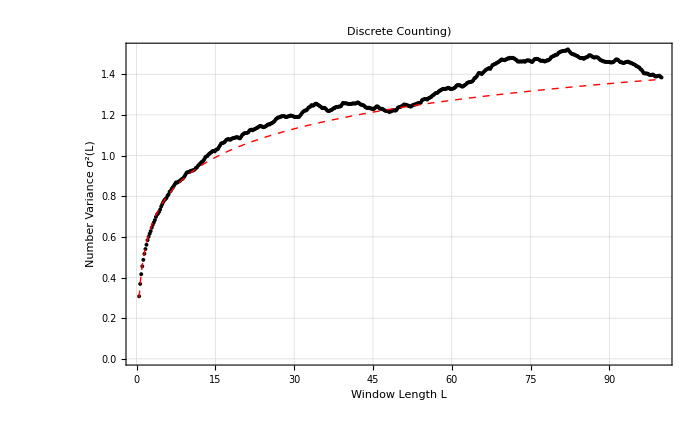

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.004]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,100,0.2}]]},ImageSize->700]
```

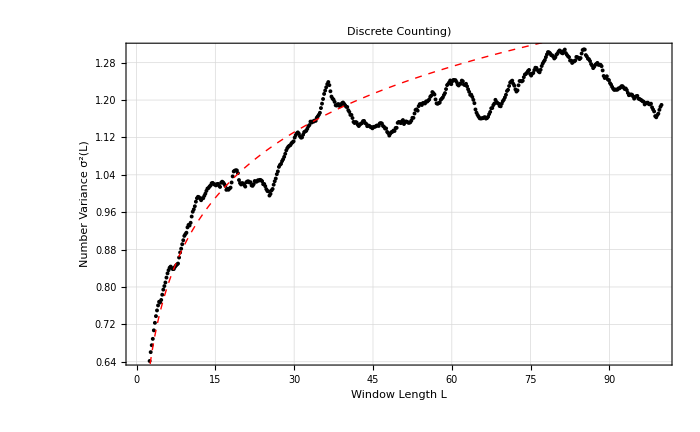

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.004]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,100,0.2}]]},ImageSize->700]
```

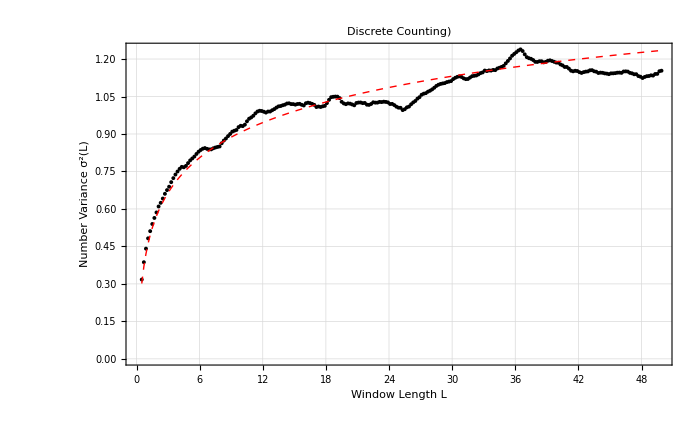

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.004]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,50,0.2}]]},ImageSize->700]
```

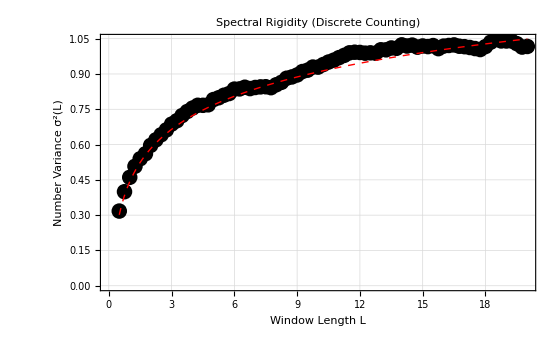

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,20,0.1}]]}]
```

```mathematica
(*4. Define Theoretical Curves*)
poisson[L_]:=L;
goe[L_]:=(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
gue[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
```

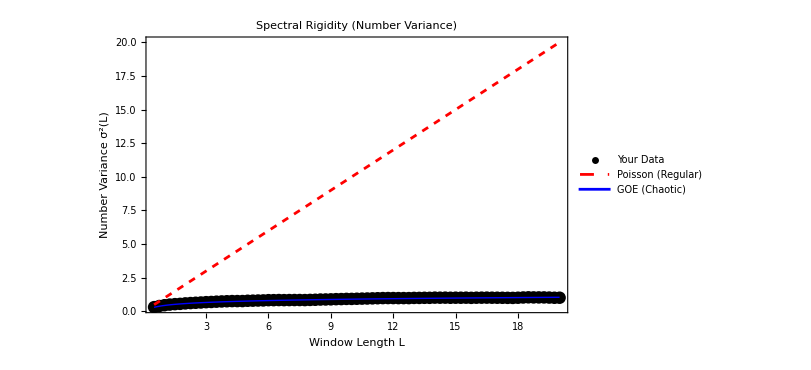

```mathematica
(*5. Plot*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{poisson[L],goe[L]},{L,0.5,20},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

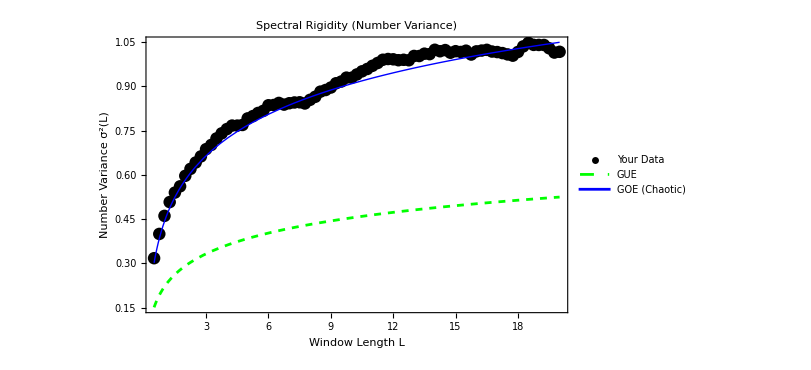

```mathematica
(*5. Plot*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{gue[L],goe[L]},{L,0.5,20},PlotStyle->{{Green,Dashed},{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

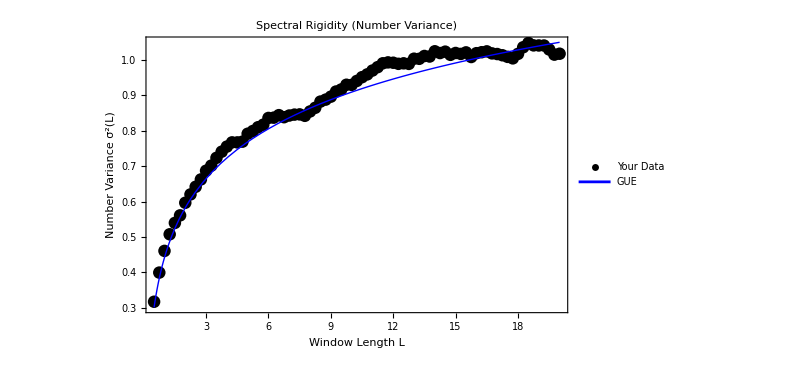

```mathematica
(*5. Plot*)
(*Positive parity*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{goe[L]},{L,0.5,20},PlotStyle->{{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

```mathematica
(*1. Define the Staircase Function*)(*Ensure'unfolded' is defined and sorted*)
nTotal=Length[unfolded];
staircaseFunc=Interpolation[Transpose[{unfolded,Range[nTotal]}],InterpolationOrder->1 ];
(*3. Parallel Calculation over L*)
LvaluesRigidity=Range[1,20,0.25]; (*Check L=1 to 20*)
```

```mathematica
(*1. Define Correct Discrete Delta3 Calculation*)(*This computes Delta3 directly from the eigenvalues in the window*)
calcDelta3Discrete[center_,L_,spectrum_]:=Module[{inWindow,n,y,term1,term2},
(*Find eigenvalues inside the window[center-L/2,center+L/2]*)
inWindow=Select[spectrum,(center-L/2<=#<=center+L/2)&];
n=Length[inWindow];
(*If window is empty,deviation is just the linear fit of nothing (0)*)
If[n==0,Return[0]];
(*Transform to relative coordinates[-L/2,L/2]*)
y=inWindow-center;
(*We use the analytical formula for Delta3 of a step function.Ref:Bohigas,Giannoni,Schmit (1984)/Standard RMT texts.It relates to the moments of the positions in the window.*)(*This is a numerically stable integration of the step function deviation*)(*Delta3=(n^2)/16-(1/L^2)*Sum[y]^2+(3/L4)*Sum[y^2] is for the "stiffness" but direct integration of (N(x)-Ax-B)^2 is safer to implement:*)(*Let's stick to the definition:Min integral (N(x)-Ax-B)^2*)(*For a step function,this integral can be solved exactly.*)(*But to be safe and fast,let's use a high-res numeric integral of a Step Function*)(1/L)*NIntegrate[(Count[inWindow,v_/;v<=x]-(n/L)*(x-(center-L/2)))^2,{x,center-L/2,center+L/2},Method->"LocalAdaptive",AccuracyGoal->5]
(*Note:The term (n/L) above is an approximation of the average slope.For the exact Delta3,we subtract the BEST fit,not the average slope.*)];
(*FASTER METHOD:discrete summation moments*)
(*This formula is exact for Delta3 of a sequence of n levels x_i in[-L/2,L/2]*)
delta3Exact[L_,spectrum_]:=Module[{M1,M2,n},n=Length[spectrum];
If[n==0,Return[L/15]];(*Poisson empty limit approximation or 0*)(*Moments of the positions relative to window center*)
M1=Total[spectrum];(*Sum x_i*)
M2=Total[spectrum^2];(*Sum x_i^2*)(*Formula for min deviation of step function*)(*Delta3=n^2/12-n/L*M1+... this is getting complex to derive on the fly.*)(*Let's Use InterpolationOrder->0 (Step) which is reliable in Mathematica*)Nothing];
(*RE-RUN with InterpolationOrder->0*)
(*This is the easiest fix for your existing workflow*)
staircaseFuncStep=Interpolation[Transpose[{unfolded,Range[Length[unfolded]]}],InterpolationOrder->0 (*STRICT STEP FUNCTION*)];
calcDelta3WindowStep[center_,L_]:=Module[{min,max,meanN,slopeTerm,x},min=center-L/2;
max=center+L/2;
(*NIntegrate handles discontinuities automatically if limits are standard*)(*1. Average Height*)meanN=NIntegrate[staircaseFuncStep[x],{x,min,max}]/L;
(*2. Slope Term (Best Fit)*)slopeTerm=(12/L^3)*NIntegrate[(x-center)*(staircaseFuncStep[x]-meanN),{x,min,max}];
(*3. Compute Variance*)(1/L)*NIntegrate[(staircaseFuncStep[x]-(meanN+slopeTerm*(x-center)))^2,{x,min,max}]];
```

```mathematica
(*Calculate*)
delta3DataCorrected=ParallelTable[Module[{centers,d3Values,eMin,eMax},
eMin=Min[unfolded]+L/2+0.5;
eMax=Max[unfolded]-L/2-0.5;
centers=Range[eMin,eMax,1.0];
d3Values=Map[calcDelta3WindowStep[#,L]&,centers];
{L,Mean[d3Values]}],{L,1,20,1},Method->"CoarsestGrained"];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$27$798126`x$8277 near {Notebook$$27$798126`x$8277} = {-488.85320078867694532684333561983375098836224312455478457906110634}. NIntegrate obtained -8.01187×10^-31 and 3.43139×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$27$798126`x$9069 near {Notebook$$27$798126`x$9069} = {-480.85320078867694532684333561983375098836224312455478457906110634}. NIntegrate obtained -1.60237×10^-30 and 6.86277×10^-30 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$27$798126`x$9554 near {Notebook$$27$798126`x$9554} = {-475.916}. NIntegrate obtained 9.7375×10^-31 and 8.23787×10^-31 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
(*Theoretical Predictions for Delta3(L) when L>>1*)(*EulerGamma is approx 0.577*)(*GOE:Time Reversal Symmetry (e.g.Standard QKT)*)
delta3GOE[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma-5/4-Pi^2/8);
(*GUE:Broken Time Reversal Symmetry*)
delta3GUE[L_]:=(1/(2*Pi^2))*(Log[2*Pi*L]+EulerGamma-5/4);
```

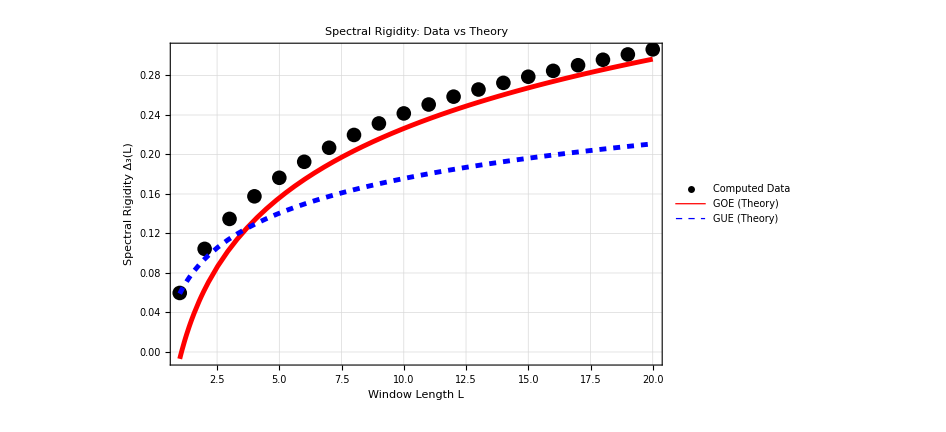

```mathematica
Show[(*Your Data*)ListPlot[delta3DataCorrected,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Computed Data"}],(*Theoretical Curves*)Plot[{delta3GOE[L],delta3GUE[L]},{L,1,20},PlotStyle->{{Red,Thickness[0.005]},{Blue,Dashed,Thickness[0.005]}},PlotLegends->{"GOE (Theory)","GUE (Theory)"}],Frame->True,FrameLabel->{"Window Length L","Spectral Rigidity \!\(\*SubscriptBox[\(Δ\), \(3\)]\)(L)"},PlotLabel->"Spectral Rigidity: Data vs Theory",GridLines->Automatic,ImageSize->700,PlotRange->All]
```

```mathematica
(*1. Define the Theoretical GOE Curve*)
Kgoe[tau_]:=If[tau<=1,2*tau-tau*Log[1+2*tau],2-tau*Log[(2*tau+1)/(2*tau-1)]];
(*2. Compute the "Raw" SFF from Unfolded Data*)
ComputeSFF[eigenvalues_,tauMax_,steps_]:=Module[{N,taus,Kraw},N=Length[eigenvalues];
taus=Range[0.01,tauMax,tauMax/steps];
(*Compute power spectrum for each time tau*)Kraw=Table[(1/N)*Abs[Sum[Exp[-I*2*Pi*e*t],{e,eigenvalues}]]^2,{t,taus}];
Transpose[{taus,Kraw}]];
(*3. CORRECTED SmoothSFF Function*)
SmoothSFF[data_,windowSize_]:=Module[{taus,kvals},taus=data[[All,1]];
kvals=data[[All,2]];
(*FIX:Apply MovingAverage to BOTH x and y to keep lengths equal and centered*)Transpose[{MovingAverage[taus,windowSize],MovingAverage[kvals,windowSize]}]];
```

```mathematica
(*---EXECUTION---*)
(*Parameters*)
tauLimit=2.0;
numPoints=2000;
smoothWindow=100; (*If the plot is still too noisy,increase this to 100*)
```

```mathematica
(*A.Calculate Raw SFF*)
sffRaw=ComputeSFF[unfolded,tauLimit,numPoints];
(*B.Smooth it*)
sffSmoothed=SmoothSFF[sffRaw,smoothWindow];
```

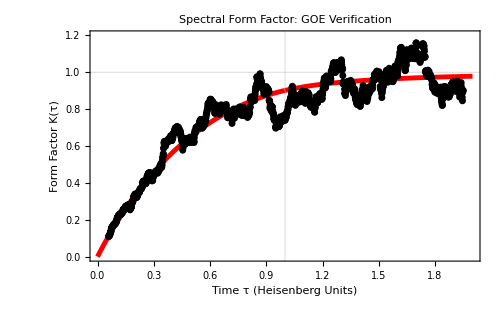

```mathematica
(*C.Plot Data vs GOE Theory*)
Show[(*Theoretical Curve (Red)*)Plot[Kgoe[tau],{tau,0,tauLimit},PlotStyle->{Red,Thickness[0.007]},PlotLabel->"Spectral Form Factor: GOE Verification"],(*Your Smoothed Data (Black)*)ListPlot[sffSmoothed,PlotStyle->{Black,PointSize[0.01]},Joined->False],Frame->True,FrameLabel->{"Time τ (Heisenberg Units)","Form Factor K(τ)"},GridLines->{{1},{1}},PlotRange->{{0,tauLimit},{0,1.2}},ImageSize->500]
```

```mathematica
SmoothSFF[data_,sigma_]:=Module[{taus,kvals},taus=data[[All,1]];
kvals=data[[All,2]];
(*GaussianFilter gives a much nicer,less jagged line*)Transpose[{taus,GaussianFilter[kvals,sigma]}]];

(*Then call it with a sigma value,e.g.,20 or 50*)
sffSmoothed=SmoothSFF[sffRaw,100];
```

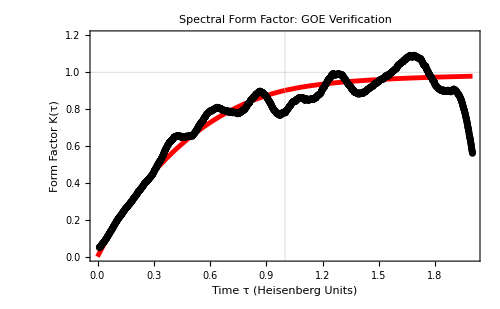

```mathematica
(*C.Plot Data vs GOE Theory*)
Show[(*Theoretical Curve (Red)*)Plot[Kgoe[tau],{tau,0,tauLimit},PlotStyle->{Red,Thickness[0.007]},PlotLabel->"Spectral Form Factor: GOE Verification"],(*Your Smoothed Data (Black)*)ListPlot[sffSmoothed,PlotStyle->{Black,PointSize[0.01]},Joined->False],Frame->True,FrameLabel->{"Time τ (Heisenberg Units)","Form Factor K(τ)"},GridLines->{{1},{1}},PlotRange->{{0,tauLimit},{0,1.2}},ImageSize->500]
```

```mathematica
(*3. Compute the Trace Power Spectrum*)
(*This is|Tr(U^t)|^2 which relates to Periodic Orbits*)
rawPhases=Arg[eigenvalM];
tMaxPO=100; (*Look at short times to see short orbits*)
powerSpectrum=Table[{t,Abs[Total[Exp[-I*t*rawPhases]]]^2},{t,1,tMaxPO}];
```

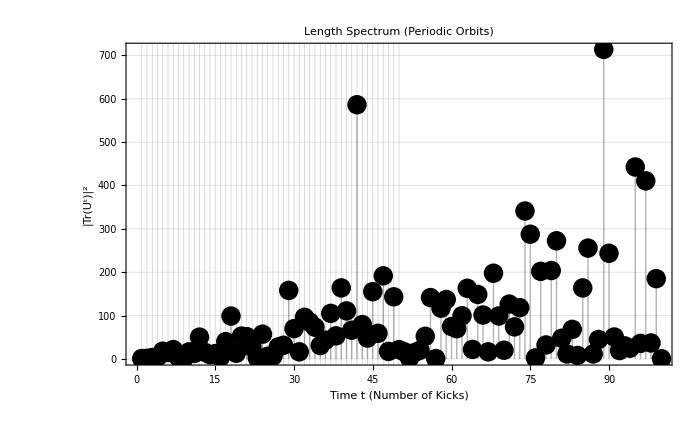

```mathematica
(*4. Plot*)
ListPlot[powerSpectrum,Filling->Axis,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Time t (Number of Kicks)","|Tr(\!\(\*SuperscriptBox[\(U\), \(t\)]\))|\!\(\*SuperscriptBox[\(\), \(2\)]\)"},PlotLabel->"Length Spectrum (Periodic Orbits)",GridLines->{Range[tMaxPO],Automatic},PlotRange->All,ImageSize->700]
```

```mathematica
dim=J+1;
(*1. Use the full time range up to system dimension*)
tMaxFull=(J+1); (*This should be 1000*)
(*2. Compute Form Factor efficiently using Eigenvalues*)
(*We use the'rawPhases' list you created earlier.*)
(*This is much faster than MatrixPower*)
kDataFull=Table[Abs[Total[Exp[-I*t*rawPhases]]]^2,{t,1,tMaxFull}];
(*3. Reconstruction Formula (Summing all the way to N)*)
reconstructedSigmaFull[L_]:=(2/Pi^2)*Sum[(kDataFull[[t]]/t^2)*Sin[(Pi*L*t)/dim]^2,{t,1,tMaxFull}];
```

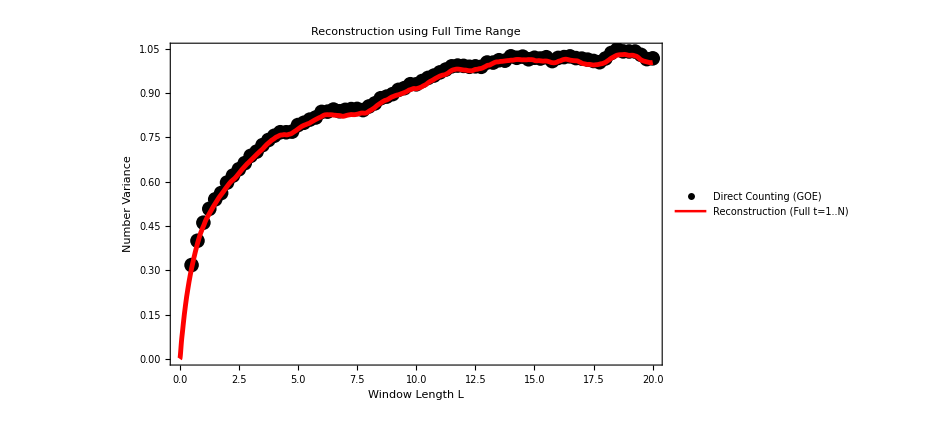

```mathematica
(*4. Plot Comparison*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Direct Counting (GOE)"}],Plot[reconstructedSigmaFull[L],{L,0,20},PlotStyle->{Red,Thickness[0.005]},PlotLegends->{"Reconstruction (Full t=1..N)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance"},PlotLabel->"Reconstruction using Full Time Range",PlotRange->All,ImageSize->700]
```

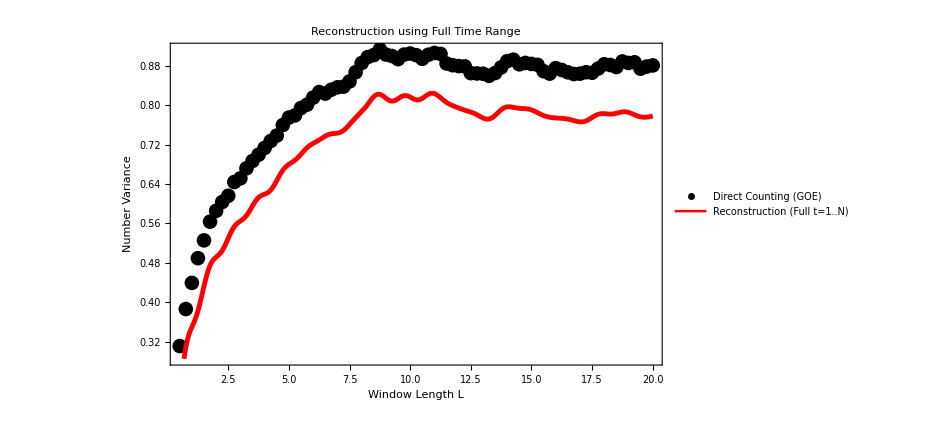

```mathematica
(*4. Plot Comparison*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Direct Counting (GOE)"}],Plot[reconstructedSigmaFull[L],{L,0,20},PlotStyle->{Red,Thickness[0.005]},PlotLegends->{"Reconstruction (Full t=1..N)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance"},PlotLabel->"Reconstruction using Full Time Range",PlotRange->All,ImageSize->700]
```

## Method, k = 100

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

```mathematica
(*Floquet parameters*)
J=1000;
d=2 J+1;
α=0.84;
k=100.;
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.532118,0.511394}

```mathematica
phases=Sort[Arg[eigenvalM]];
(*2. Create a list of {phase,index} pairs*)
(*The index runs from 1 to the total number of eigenvalues*)
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

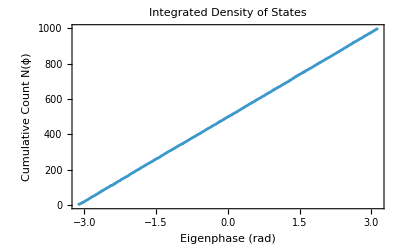

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

```mathematica
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

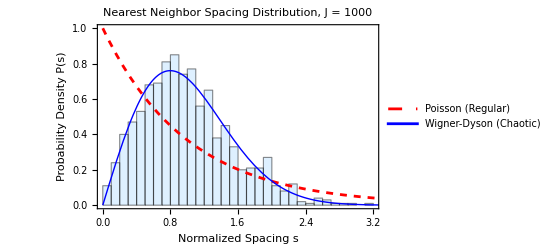

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

```mathematica
(*1. Create an efficient counting function using Interpolation*)(*This maps energy->index.n(E)*)
n=Length[unfolded];
staircase=Interpolation[Transpose[{unfolded,Range[n]}],InterpolationOrder->1];
```

```mathematica
(*2. Define the range of L and the spectrum boundaries*)
eMin=Min[unfolded];
eMax=Max[unfolded];
Lvalues=Range[0.5,20.0,0.25];
(*crucial:'unfolded' must be defined before running this*)
DistributeDefinitions[unfolded];
```

```mathematica
(*3. Parallel Calculation of Sigma^2(L)*)
sigmaData=ParallelTable[Module[{centers,counts,eMin,eMax},
eMin=Min[unfolded];
eMax=Max[unfolded];
(*Define centers for the sliding window*)(*Step size 0.2 gives good statistics without being too slow*)
centers=Range[eMin+L/2,eMax-L/2,0.2];
(*Count how many levels fall in each window*)
counts=Table[Count[unfolded,x_/;(c-L/2<=x<=c+L/2)],{c,centers}];
(*Return the pair {L,Variance}*)
{L,Variance[counts]}],{L,Lvalues},Method->"CoarsestGrained"];
```

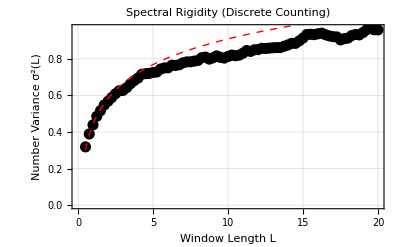

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,20,0.1}]]}]
```

```mathematica
(*4. Define Theoretical Curves*)
poisson[L_]:=L;
goe[L_]:=(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
gue[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
```

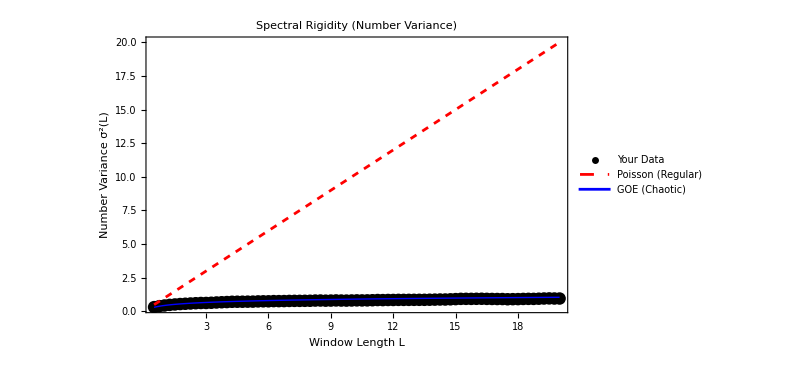

```mathematica
(*5. Plot*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{poisson[L],goe[L]},{L,0.5,20},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

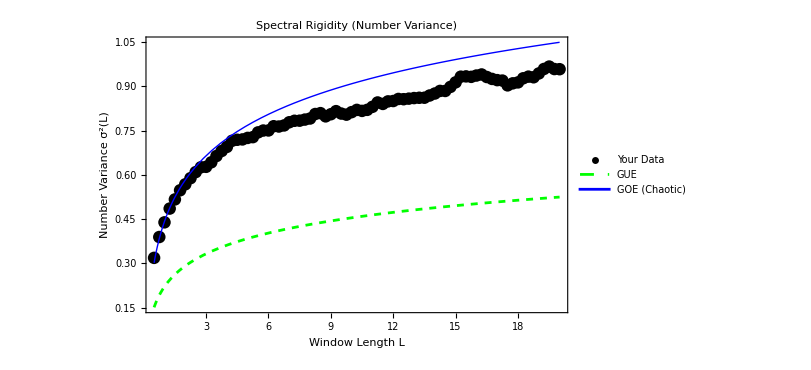

```mathematica
(*5. Plot*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{gue[L],goe[L]},{L,0.5,20},PlotStyle->{{Green,Dashed},{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

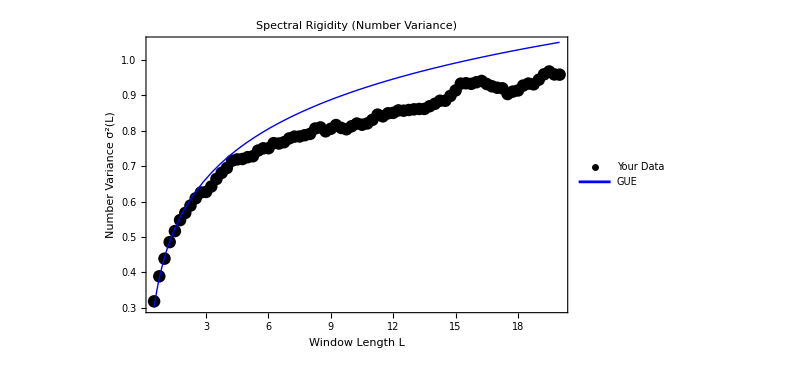

```mathematica
(*5. Plot*)
(*Positive parity*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{goe[L]},{L,0.5,20},PlotStyle->{{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

```mathematica
(*1. Define the Staircase Function*)(*Ensure'unfolded' is defined and sorted*)
nTotal=Length[unfolded];
staircaseFunc=Interpolation[Transpose[{unfolded,Range[nTotal]}],InterpolationOrder->1 ];
(*3. Parallel Calculation over L*)
LvaluesRigidity=Range[1,20,0.25]; (*Check L=1 to 20*)
```

```mathematica
(*1. Define Correct Discrete Delta3 Calculation*)(*This computes Delta3 directly from the eigenvalues in the window*)calcDelta3Discrete[center_,L_,spectrum_]:=Module[{inWindow,n,y,term1,term2},(*Find eigenvalues inside the window[center-L/2,center+L/2]*)inWindow=Select[spectrum,(center-L/2<=#<=center+L/2)&];
n=Length[inWindow];
(*If window is empty,deviation is just the linear fit of nothing (0)*)If[n==0,Return[0]];
(*Transform to relative coordinates[-L/2,L/2]*)y=inWindow-center;
(*We use the analytical formula for Delta3 of a step function.Ref:Bohigas,Giannoni,Schmit (1984)/Standard RMT texts.It relates to the moments of the positions in the window.*)(*This is a numerically stable integration of the step function deviation*)(*Delta3=(n^2)/16-(1/L^2)*Sum[y]^2+(3/L4)*Sum[y^2] is for the "stiffness" but direct integration of (N(x)-Ax-B)^2 is safer to implement:*)(*Let's stick to the definition:Min integral (N(x)-Ax-B)^2*)(*For a step function,this integral can be solved exactly.*)(*But to be safe and fast,let's use a high-res numeric integral of a Step Function*)(1/L)*NIntegrate[(Count[inWindow,v_/;v<=x]-(n/L)*(x-(center-L/2)))^2,{x,center-L/2,center+L/2},Method->"LocalAdaptive",AccuracyGoal->5]
(*Note:The term (n/L) above is an approximation of the average slope.For the exact Delta3,we subtract the BEST fit,not the average slope.*)];
(*FASTER METHOD:discrete summation moments*)
(*This formula is exact for Delta3 of a sequence of n levels x_i in[-L/2,L/2]*)
delta3Exact[L_,spectrum_]:=Module[{M1,M2,n},n=Length[spectrum];
If[n==0,Return[L/15]];(*Poisson empty limit approximation or 0*)(*Moments of the positions relative to window center*)M1=Total[spectrum];(*Sum x_i*)M2=Total[spectrum^2];(*Sum x_i^2*)(*Formula for min deviation of step function*)(*Delta3=n^2/12-n/L*M1+... this is getting complex to derive on the fly.*)(*Let's Use InterpolationOrder->0 (Step) which is reliable in Mathematica*)Nothing];
(*RE-RUN with InterpolationOrder->0*)
(*This is the easiest fix for your existing workflow*)
staircaseFuncStep=Interpolation[Transpose[{unfolded,Range[Length[unfolded]]}],InterpolationOrder->0 (*STRICT STEP FUNCTION*)];
calcDelta3WindowStep[center_,L_]:=Module[{min,max,meanN,slopeTerm,x},min=center-L/2;
max=center+L/2;
(*NIntegrate handles discontinuities automatically if limits are standard*)(*1. Average Height*)meanN=NIntegrate[staircaseFuncStep[x],{x,min,max}]/L;
(*2. Slope Term (Best Fit)*)slopeTerm=(12/L^3)*NIntegrate[(x-center)*(staircaseFuncStep[x]-meanN),{x,min,max}];
(*3. Compute Variance*)(1/L)*NIntegrate[(staircaseFuncStep[x]-(meanN+slopeTerm*(x-center)))^2,{x,min,max}]];
```

```mathematica
(*Calculate*)
delta3DataCorrected=ParallelTable[Module[{centers,d3Values,eMin,eMax},eMin=Min[unfolded]+L/2+0.5;
eMax=Max[unfolded]-L/2-0.5;
centers=Range[eMin,eMax,1.0];
d3Values=Map[calcDelta3WindowStep[#,L]&,centers];
{L,Mean[d3Values]}],{L,1,20,1},Method->"CoarsestGrained"];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$32$736588`x$9000 near {Notebook$$32$736588`x$9000} = {-487.81133027394851537403235151496200111043255562455478457906110634}. NIntegrate obtained -8.01187×10^-31 and 3.43139×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$32$736588`x$12408 near {Notebook$$32$736588`x$12408} = {-452.81133027394851537403235151496200111043255562455478457906110634}. NIntegrate obtained -3.20475×10^-30 and 1.37255×10^-29 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$32$736588`x$12696 near {Notebook$$32$736588`x$12696} = {-449.874}. NIntegrate obtained 1.9475×10^-30 and 1.64757×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
(*Theoretical Predictions for Delta3(L) when L>>1*)(*EulerGamma is approx 0.577*)(*GOE:Time Reversal Symmetry (e.g.Standard QKT)*)
delta3GOE[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma-5/4-Pi^2/8);
(*GUE:Broken Time Reversal Symmetry*)
delta3GUE[L_]:=(1/(2*Pi^2))*(Log[2*Pi*L]+EulerGamma-5/4);
```

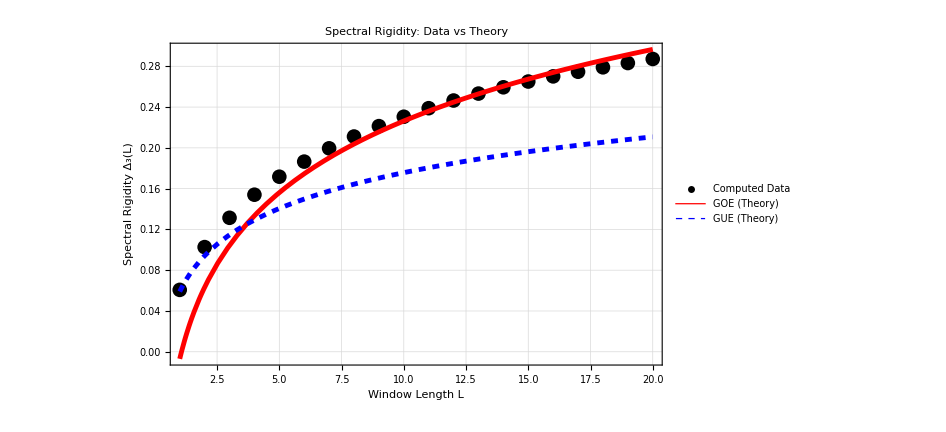

```mathematica
Show[(*Your Data*)ListPlot[delta3DataCorrected,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Computed Data"}],(*Theoretical Curves*)Plot[{delta3GOE[L],delta3GUE[L]},{L,1,20},PlotStyle->{{Red,Thickness[0.005]},{Blue,Dashed,Thickness[0.005]}},PlotLegends->{"GOE (Theory)","GUE (Theory)"}],Frame->True,FrameLabel->{"Window Length L","Spectral Rigidity \!\(\*SubscriptBox[\(Δ\), \(3\)]\)(L)"},PlotLabel->"Spectral Rigidity: Data vs Theory",GridLines->Automatic,ImageSize->700,PlotRange->All]
```

```mathematica
(*1. Define the Theoretical GOE Curve*)
Kgoe[tau_]:=If[tau<=1,2*tau-tau*Log[1+2*tau],2-tau*Log[(2*tau+1)/(2*tau-1)]];
(*2. Compute the "Raw" SFF from Unfolded Data*)
ComputeSFF[eigenvalues_,tauMax_,steps_]:=Module[{N,taus,Kraw},N=Length[eigenvalues];
taus=Range[0.01,tauMax,tauMax/steps];
(*Compute power spectrum for each time tau*)Kraw=Table[(1/N)*Abs[Sum[Exp[-I*2*Pi*e*t],{e,eigenvalues}]]^2,{t,taus}];
Transpose[{taus,Kraw}]];
(*3. CORRECTED SmoothSFF Function*)
SmoothSFF[data_,windowSize_]:=Module[{taus,kvals},taus=data[[All,1]];
kvals=data[[All,2]];
(*FIX:Apply MovingAverage to BOTH x and y to keep lengths equal and centered*)Transpose[{MovingAverage[taus,windowSize],MovingAverage[kvals,windowSize]}]];
```

```mathematica
(*---EXECUTION---*)
(*Parameters*)
tauLimit=2.0;
numPoints=2000;
smoothWindow=100; (*If the plot is still too noisy,increase this to 100*)
```

```mathematica
(*A.Calculate Raw SFF*)
sffRaw=ComputeSFF[unfolded,tauLimit,numPoints];
(*B.Smooth it*)
sffSmoothed=SmoothSFF[sffRaw,smoothWindow];
```

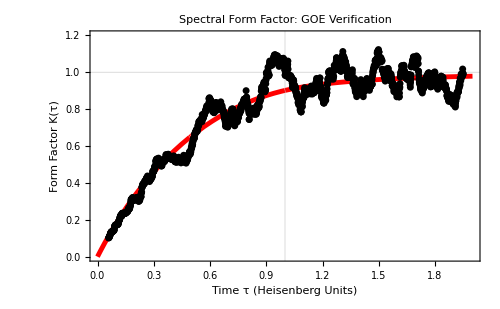

```mathematica
(*C.Plot Data vs GOE Theory*)
Show[(*Theoretical Curve (Red)*)Plot[Kgoe[tau],{tau,0,tauLimit},PlotStyle->{Red,Thickness[0.007]},PlotLabel->"Spectral Form Factor: GOE Verification"],(*Your Smoothed Data (Black)*)ListPlot[sffSmoothed,PlotStyle->{Black,PointSize[0.01]},Joined->False],Frame->True,FrameLabel->{"Time τ (Heisenberg Units)","Form Factor K(τ)"},GridLines->{{1},{1}},PlotRange->{{0,tauLimit},{0,1.2}},ImageSize->500]
```

## Method, k = 1000

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

```mathematica
(*Floquet parameters*)
J=1000;
d=2 J+1;
α=0.84;
k=1000.;
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.535369,0.542532}

```mathematica
phases=Sort[Arg[eigenvalM]];
(*2. Create a list of {phase,index} pairs*)
(*The index runs from 1 to the total number of eigenvalues*)
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

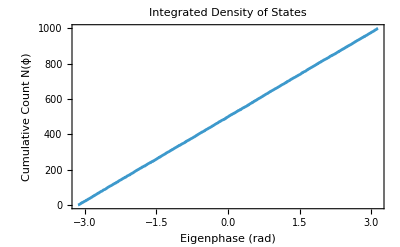

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

```mathematica
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

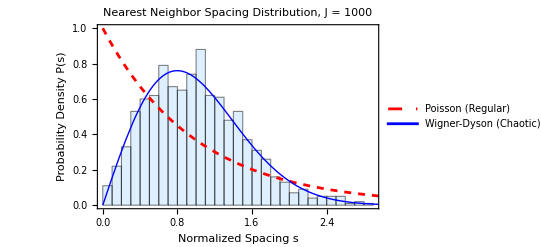

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

```mathematica
(*1. Create an efficient counting function using Interpolation*)(*This maps energy->index.n(E)*)
n=Length[unfolded];
staircase=Interpolation[Transpose[{unfolded,Range[n]}],InterpolationOrder->1];
```

```mathematica
(*2. Define the range of L and the spectrum boundaries*)
eMin=Min[unfolded];
eMax=Max[unfolded];
Lvalues=Range[0.5,20.0,0.25];
(*crucial:'unfolded' must be defined before running this*)
DistributeDefinitions[unfolded];
```

```mathematica
(*3. Parallel Calculation of Sigma^2(L)*)
sigmaData=ParallelTable[Module[{centers,counts,eMin,eMax},
eMin=Min[unfolded];
eMax=Max[unfolded];
(*Define centers for the sliding window*)(*Step size 0.2 gives good statistics without being too slow*)
centers=Range[eMin+L/2,eMax-L/2,0.2];
(*Count how many levels fall in each window*)
counts=Table[Count[unfolded,x_/;(c-L/2<=x<=c+L/2)],{c,centers}];
(*Return the pair {L,Variance}*)
{L,Variance[counts]}],{L,Lvalues},Method->"CoarsestGrained"];
```

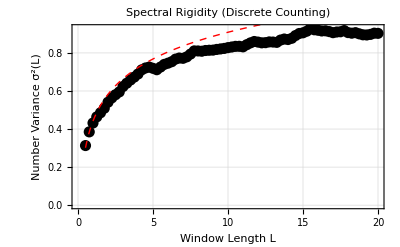

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,20,0.1}]]}]
```

```mathematica
(*4. Define Theoretical Curves*)
poisson[L_]:=L;
goe[L_]:=(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
gue[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
```

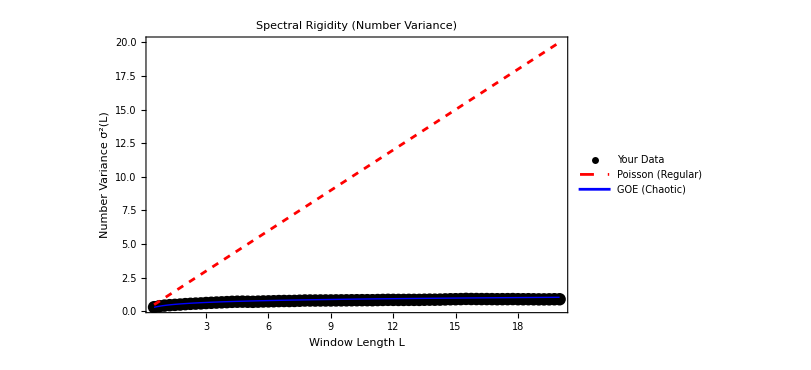

```mathematica
(*5. Plot*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{poisson[L],goe[L]},{L,0.5,20},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

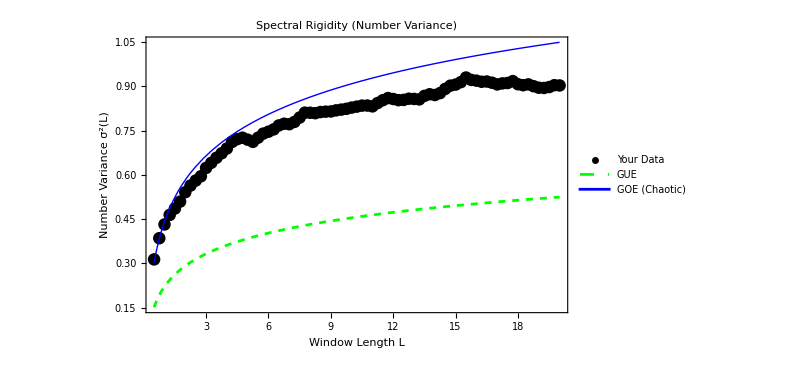

```mathematica
(*5. Plot*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{gue[L],goe[L]},{L,0.5,20},PlotStyle->{{Green,Dashed},{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

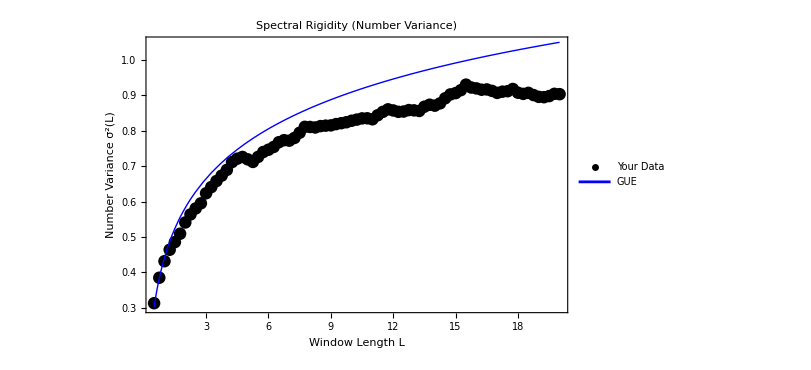

```mathematica
(*5. Plot*)
(*Positive parity*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{goe[L]},{L,0.5,20},PlotStyle->{{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

```mathematica
(*1. Define the Staircase Function*)(*Ensure'unfolded' is defined and sorted*)
nTotal=Length[unfolded];
staircaseFunc=Interpolation[Transpose[{unfolded,Range[nTotal]}],InterpolationOrder->1 ];
(*3. Parallel Calculation over L*)
LvaluesRigidity=Range[1,20,0.25]; (*Check L=1 to 20*)
```

```mathematica
(*1. Define Correct Discrete Delta3 Calculation*)(*This computes Delta3 directly from the eigenvalues in the window*)calcDelta3Discrete[center_,L_,spectrum_]:=Module[{inWindow,n,y,term1,term2},(*Find eigenvalues inside the window[center-L/2,center+L/2]*)inWindow=Select[spectrum,(center-L/2<=#<=center+L/2)&];
n=Length[inWindow];
(*If window is empty,deviation is just the linear fit of nothing (0)*)If[n==0,Return[0]];
(*Transform to relative coordinates[-L/2,L/2]*)y=inWindow-center;
(*We use the analytical formula for Delta3 of a step function.Ref:Bohigas,Giannoni,Schmit (1984)/Standard RMT texts.It relates to the moments of the positions in the window.*)(*This is a numerically stable integration of the step function deviation*)(*Delta3=(n^2)/16-(1/L^2)*Sum[y]^2+(3/L4)*Sum[y^2] is for the "stiffness" but direct integration of (N(x)-Ax-B)^2 is safer to implement:*)(*Let's stick to the definition:Min integral (N(x)-Ax-B)^2*)(*For a step function,this integral can be solved exactly.*)(*But to be safe and fast,let's use a high-res numeric integral of a Step Function*)(1/L)*NIntegrate[(Count[inWindow,v_/;v<=x]-(n/L)*(x-(center-L/2)))^2,{x,center-L/2,center+L/2},Method->"LocalAdaptive",AccuracyGoal->5]
(*Note:The term (n/L) above is an approximation of the average slope.For the exact Delta3,we subtract the BEST fit,not the average slope.*)];
(*FASTER METHOD:discrete summation moments*)
(*This formula is exact for Delta3 of a sequence of n levels x_i in[-L/2,L/2]*)
delta3Exact[L_,spectrum_]:=Module[{M1,M2,n},n=Length[spectrum];
If[n==0,Return[L/15]];(*Poisson empty limit approximation or 0*)(*Moments of the positions relative to window center*)M1=Total[spectrum];(*Sum x_i*)M2=Total[spectrum^2];(*Sum x_i^2*)(*Formula for min deviation of step function*)(*Delta3=n^2/12-n/L*M1+... this is getting complex to derive on the fly.*)(*Let's Use InterpolationOrder->0 (Step) which is reliable in Mathematica*)Nothing];
(*RE-RUN with InterpolationOrder->0*)
(*This is the easiest fix for your existing workflow*)
staircaseFuncStep=Interpolation[Transpose[{unfolded,Range[Length[unfolded]]}],InterpolationOrder->0 (*STRICT STEP FUNCTION*)];
calcDelta3WindowStep[center_,L_]:=Module[{min,max,meanN,slopeTerm,x},min=center-L/2;
max=center+L/2;
(*NIntegrate handles discontinuities automatically if limits are standard*)(*1. Average Height*)meanN=NIntegrate[staircaseFuncStep[x],{x,min,max}]/L;
(*2. Slope Term (Best Fit)*)slopeTerm=(12/L^3)*NIntegrate[(x-center)*(staircaseFuncStep[x]-meanN),{x,min,max}];
(*3. Compute Variance*)(1/L)*NIntegrate[(staircaseFuncStep[x]-(meanN+slopeTerm*(x-center)))^2,{x,min,max}]];
```

```mathematica
(*Calculate*)
delta3DataCorrected=ParallelTable[Module[{centers,d3Values,eMin,eMax},eMin=Min[unfolded]+L/2+0.5;
eMax=Max[unfolded]-L/2-0.5;
centers=Range[eMin,eMax,1.0];
d3Values=Map[calcDelta3WindowStep[#,L]&,centers];
{L,Mean[d3Values]}],{L,1,20,1},Method->"CoarsestGrained"];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$32$736588`x$205159 near {Notebook$$32$736588`x$205159} = {-492.394}. NIntegrate obtained 2.43438×10^-31 and 2.05947×10^-31 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$32$736588`x$205647 near {Notebook$$32$736588`x$205647} = {-487.394}. NIntegrate obtained 4.86875×10^-31 and 4.11894×10^-31 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$32$736588`x$208069 near {Notebook$$32$736588`x$208069} = {-462.394}. NIntegrate obtained 9.7375×10^-31 and 8.23787×10^-31 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
(*Theoretical Predictions for Delta3(L) when L>>1*)(*EulerGamma is approx 0.577*)(*GOE:Time Reversal Symmetry (e.g.Standard QKT)*)
delta3GOE[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma-5/4-Pi^2/8);
(*GUE:Broken Time Reversal Symmetry*)
delta3GUE[L_]:=(1/(2*Pi^2))*(Log[2*Pi*L]+EulerGamma-5/4);
```

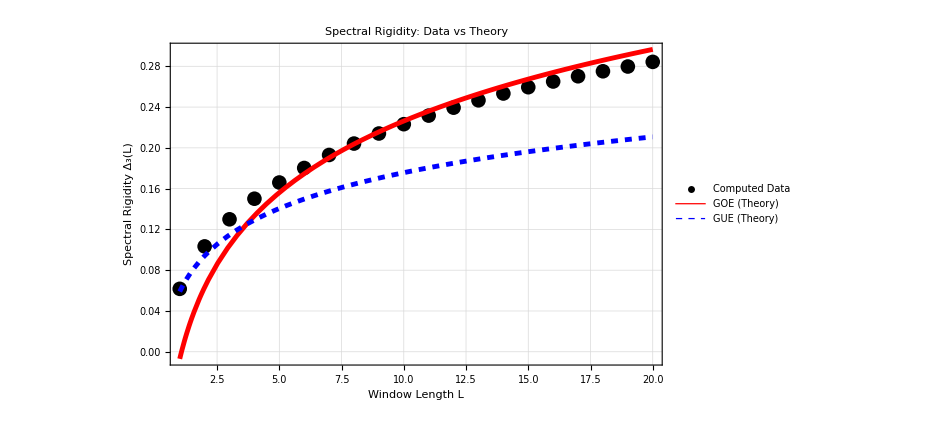

```mathematica
Show[(*Your Data*)ListPlot[delta3DataCorrected,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Computed Data"}],(*Theoretical Curves*)Plot[{delta3GOE[L],delta3GUE[L]},{L,1,20},PlotStyle->{{Red,Thickness[0.005]},{Blue,Dashed,Thickness[0.005]}},PlotLegends->{"GOE (Theory)","GUE (Theory)"}],Frame->True,FrameLabel->{"Window Length L","Spectral Rigidity \!\(\*SubscriptBox[\(Δ\), \(3\)]\)(L)"},PlotLabel->"Spectral Rigidity: Data vs Theory",GridLines->Automatic,ImageSize->700,PlotRange->All]
```

```mathematica
(*1. Define the Theoretical GOE Curve*)
Kgoe[tau_]:=If[tau<=1,2*tau-tau*Log[1+2*tau],2-tau*Log[(2*tau+1)/(2*tau-1)]];
(*2. Compute the "Raw" SFF from Unfolded Data*)
ComputeSFF[eigenvalues_,tauMax_,steps_]:=Module[{N,taus,Kraw},N=Length[eigenvalues];
taus=Range[0.01,tauMax,tauMax/steps];
(*Compute power spectrum for each time tau*)Kraw=Table[(1/N)*Abs[Sum[Exp[-I*2*Pi*e*t],{e,eigenvalues}]]^2,{t,taus}];
Transpose[{taus,Kraw}]];
(*3. CORRECTED SmoothSFF Function*)
SmoothSFF[data_,windowSize_]:=Module[{taus,kvals},taus=data[[All,1]];
kvals=data[[All,2]];
(*FIX:Apply MovingAverage to BOTH x and y to keep lengths equal and centered*)Transpose[{MovingAverage[taus,windowSize],MovingAverage[kvals,windowSize]}]];
```

```mathematica
(*---EXECUTION---*)
(*Parameters*)
tauLimit=2.0;
numPoints=2000;
smoothWindow=100; (*If the plot is still too noisy,increase this to 100*)
```

```mathematica
(*A.Calculate Raw SFF*)
sffRaw=ComputeSFF[unfolded,tauLimit,numPoints];
(*B.Smooth it*)
sffSmoothed=SmoothSFF[sffRaw,smoothWindow];
```

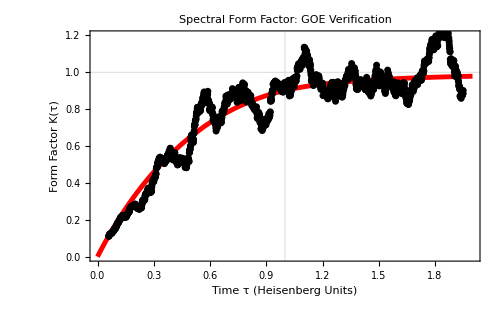

```mathematica
(*C.Plot Data vs GOE Theory*)
Show[(*Theoretical Curve (Red)*)Plot[Kgoe[tau],{tau,0,tauLimit},PlotStyle->{Red,Thickness[0.007]},PlotLabel->"Spectral Form Factor: GOE Verification"],(*Your Smoothed Data (Black)*)ListPlot[sffSmoothed,PlotStyle->{Black,PointSize[0.01]},Joined->False],Frame->True,FrameLabel->{"Time τ (Heisenberg Units)","Form Factor K(τ)"},GridLines->{{1},{1}},PlotRange->{{0,tauLimit},{0,1.2}},ImageSize->500]
```

## Length spectrum

```mathematica
(*3. Compute the Trace Power Spectrum*)
(*This is|Tr(U^t)|^2 which relates to Periodic Orbits*)
rawPhases=Arg[eigenvalM];
tMaxPO=100; (*Look at short times to see short orbits*)
powerSpectrum=Table[{t,Abs[Total[Exp[-I*t*rawPhases]]]^2},{t,1,tMaxPO}];
```

```mathematica
(*4. Plot*)
ListPlot[powerSpectrum,Filling->Axis,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Time t (Number of Kicks)","|Tr(\!\(\*SuperscriptBox[\(U\), \(t\)]\))|\!\(\*SuperscriptBox[\(\), \(2\)]\)"},PlotLabel->"Length Spectrum (Periodic Orbits)",GridLines->{Range[tMaxPO],Automatic},PlotRange->All,ImageSize->700]
```

-Graphics-

```mathematica
dim=J+1;
(*1. Use the full time range up to system dimension*)
tMaxFull=10(J+1); (*This should be 1000*)
(*2. Compute Form Factor efficiently using Eigenvalues*)
(*We use the'rawPhases' list you created earlier.*)
(*This is much faster than MatrixPower*)
kDataFull=Table[Abs[Total[Exp[-I*t*rawPhases]]]^2,{t,1,tMaxFull}];
(*3. Reconstruction Formula (Summing all the way to N)*)
reconstructedSigmaFull[L_]:=(2/Pi^2)*Sum[(kDataFull[[t]]/t^2)*Sin[(Pi*L*t)/dim]^2,{t,1,tMaxFull}];
```

```mathematica
(*4. Plot Comparison*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Direct Counting (GOE)"}],Plot[reconstructedSigmaFull[L],{L,0,20},PlotStyle->{Red,Thickness[0.005]},PlotLegends->{"Reconstruction (Full t=1..N)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance"},PlotLabel->"Reconstruction using Full Time Range",PlotRange->All,ImageSize->700]
```

-Graphics-

# Resonant spectrum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Breaking time reversal symmetry\\QKT.wl"];
```

```mathematica
LaunchKernels[14]
```

## Method

```mathematica
Names["QKT`*"]
```

{Floq,Floqb,Floqbn,Floqn,Floqsym,generateCoherentStateCompiler,generateSpinOperators,MeanLevelSpacingRatio}

```mathematica
(*Floquet parameters*)
J=100;
d=2 J+1;
α=1.099;
(*k=J*2Pi/5.;*)
k=J*Pi(2/5.);
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.330642,0.318213}

```mathematica
DistributeDefinitions[Floq,J,k,MeanLevelSpacingRatio];
```

```mathematica
alist=Range[0,Pi,Pi/100.];
```

```mathematica
(*2. Run in Parallel*)
rvalues=ParallelTable[Module[{mat,matM,matm,evalM,evalm},
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
evalM=Eigenvalues[matM];
evalm=Eigenvalues[matm];
{a,Quiet[MeanLevelSpacingRatio[Sort[Arg[evalM]]]],Quiet[MeanLevelSpacingRatio[Sort[Arg[evalm]]]]}],{a,alist},Method->"CoarsestGrained"];
```

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

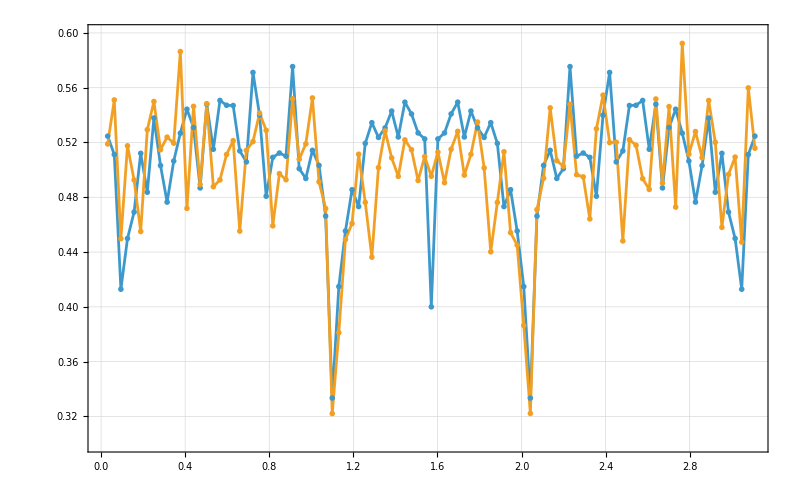

```mathematica
ListPlot[{Transpose[{rvalues[[All,1]],rvalues[[All,2]]}],Transpose[{rvalues[[All,1]],rvalues[[All,3]]}]},PlotTheme->"Detailed",Joined->True,PlotMarkers->"OpenMarkers",ImageSize->800,PlotRange->{All,{0.30,0.6}}]
```

```mathematica
(*Floquet parameters*)
J=100;
d=2 J+1;
```

```mathematica
p=2;
q=5.;
k=(p/q)J*Pi;
k=0.;
```

```mathematica
alist=Range[0,Pi,Pi/1500];
alist//Length
```

1501

```mathematica
DistributeDefinitions[Floq,J,k,MeanLevelSpacingRatio];
```

```mathematica
results=ParallelTable[Module[{mat,matM,matm,valM,valm},
mat=Floq[J,a,N[k]];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
valM=Eigenvalues[matM];
valm=Eigenvalues[matm];
{Transpose[{ConstantArray[a,Length[valM]],Arg[valM]}],Transpose[{ConstantArray[a,Length[valm]],Arg[valm]}]}],{a,alist},Method->"CoarsestGrained" ];
{levelsM,levelsm}=Transpose[results];
```

```mathematica
CustomPiTicks[d_]:=Table[{k*Pi/d,If[k==0,"0",If[k==d,"",Row[{Rationalize[k/d],""}]]]},{k,0,d+1}];
(*Generate ticks for Pi/20*)
myTicks=CustomPiTicks[20];
```

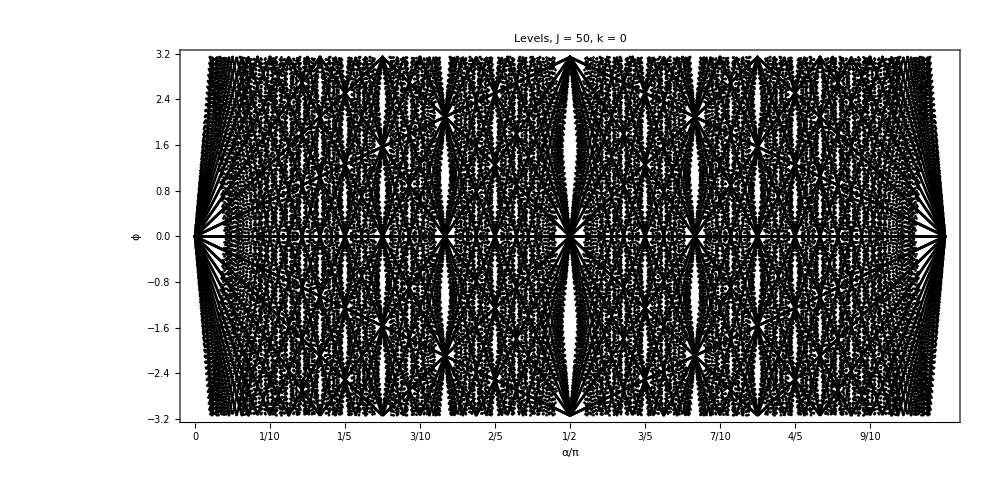

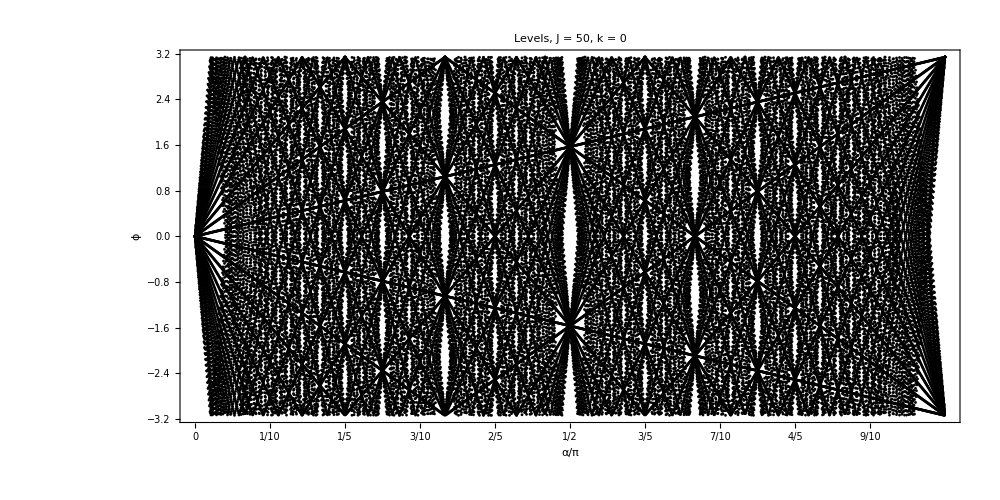

```mathematica
ListPlot[{Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = 0"}],25,Black],AspectRatio->0.5,ImageSize->1000]
ListPlot[{Flatten[levelsm,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = 0"}],25,Black],AspectRatio->0.5,ImageSize->1000]
```

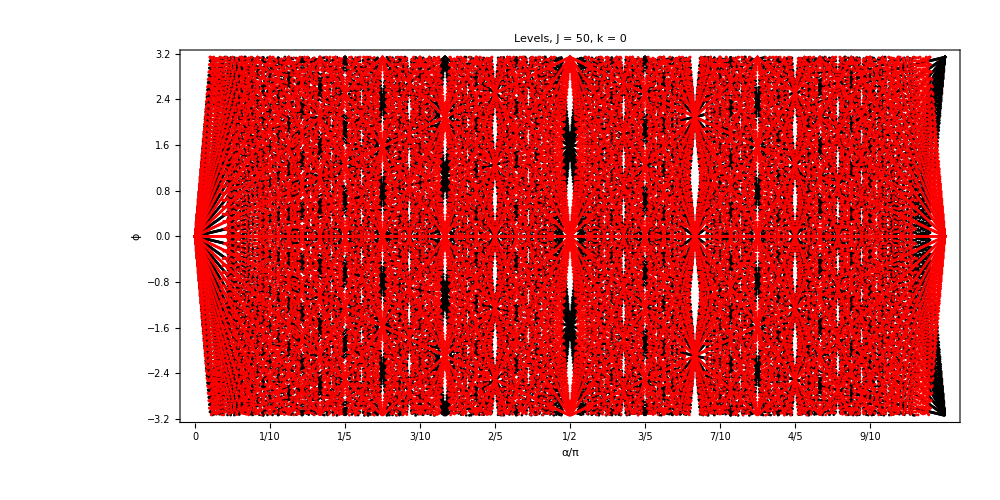

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = 0"}],25,Black],AspectRatio->0.5,ImageSize->1000]
```

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],AspectRatio->0.5,ImageSize->1000]
```

-Graphics-

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],AspectRatio->0.5,ImageSize->1000]
```

-Graphics-

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],AspectRatio->0.5,ImageSize->1000]
```

-Graphics-

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],AspectRatio->0.5,ImageSize->1000]
```

-Graphics-

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],AspectRatio->0.5,ImageSize->1000]
```

-Graphics-

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.003]],Directive[Red,PointSize[0.003]]},Axes->False,Frame->True,PlotRange->All,ImageSize->800,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black]]
```

-Graphics-

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.002]],Directive[Red,PointSize[0.002]]},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["α/π",30,Black],Style["ϕ",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLines->{myTicks[[All,1]],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],AspectRatio->0.5,ImageSize->1000]
```

-Graphics-

```mathematica
J=50;
```

```mathematica
(*1. Generate first 200 rational fractions p/q ordered by denominator*)
rationalFractions={};
q=1;
While[Length[rationalFractions]<20,Do[If[GCD[p,q]==1,AppendTo[rationalFractions,p/q]],{p,1,q}];
q++;];
rationalFractions=Take[rationalFractions,15];
```

```mathematica
alist=Range[0,Pi,Pi/1000.];
alist//Length
```

1001

```mathematica
dir="Levels";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
DistributeDefinitions[Floq,J,alist,rationalFractions];
```

```mathematica
Do[Module[{p,q,k,rawData,levelsM,levelsm,plot,filename},
p=Numerator[rationalFractions[[i]]];
q=Denominator[rationalFractions[[i]]];
k=N[Pi*J*rationalFractions[[i]]];
Print["Processing p = "<>ToString[p]<>", q = "<>ToString[q]<>"..."];
rawData=ParallelTable[Module[{mat,matM,matm,valM,valm},
mat=Floq[J,a,k];
(*mat=MatrixPower[Floq[J,a,k],q];*)
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
valM=Eigenvalues[matM];
valm=Eigenvalues[matm];
{Transpose[{ConstantArray[a,Length[valM]],Arg[valM]}],Transpose[{ConstantArray[a,Length[valm]],Arg[valm]}]}]
,{a,alist},Method->"CoarsestGrained"];

{levelsM,levelsm}=Transpose[rawData];
levelsM=Flatten[levelsM,1];
levelsm=Flatten[levelsm,1];
plot=ListPlot[{levelsm,levelsM},PlotStyle->{Directive[Black,PointSize[0.0018]],Directive[Red,PointSize[0.0018]]},PlotRange->All,ImageSize->1000,PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],Frame->True,FrameLabel->{"α","ϕ"},FrameStyle->Directive[Black,20],Axes->True,AxesStyle->Directive[Black, 15]];
filename=FileNameJoin[{dir,"levels_J_"<>ToString[J]<>"_k_"<>ToString[NumberForm[N[k],{3,2}]]<>"_p_"<>ToString[p]<>"_q_"<>ToString[q]<>".png"}];
Export[filename,plot];],{i,1,Length[rationalFractions]}];
```

Processing p = 1, q = 1...

Processing p = 1, q = 2...

Processing p = 1, q = 3...

Processing p = 2, q = 3...

Processing p = 1, q = 4...

Processing p = 3, q = 4...

Processing p = 1, q = 5...

Processing p = 2, q = 5...

Processing p = 3, q = 5...

Processing p = 4, q = 5...

Processing p = 1, q = 6...

Processing p = 5, q = 6...

Processing p = 1, q = 7...

Processing p = 2, q = 7...

Processing p = 3, q = 7...

## resonant k

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

```mathematica
(*Floquet parameters*)
J=1000;
d=2 J+1;
α=7/20.;
k=(2/5.)J*Pi;
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.5371,0.516492}

```mathematica
phases=Sort[Arg[eigenvalM]];
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

-Graphics-

```mathematica
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

-Graphics-

```mathematica
(*1. Sort Data& Define N*)
rawPhases=Sort[Mod[Arg[eigenvalM],2*Pi,-Pi]];
n=Length[rawPhases];
(*2. Define the Staircase*)
dataPairs=Transpose[{rawPhases,Range[0.5,n-0.5]}];
```

```mathematica
(*3. Fit the Smooth Part (The "Mean" Motion)*)
(*We use a low-order polynomial to capture the trend seen in your image*)
smoothFit=LinearModelFit[dataPairs,{phi,phi^3,phi^5},phi];
```

```mathematica
(*OPTIONAL:Visual Check*)
(*Make sure the Red line cuts through the "wiggles" smoothly*)
Show[ListPlot[dataPairs,PlotStyle->{Black,Tiny}],Plot[smoothFit[phi],{phi,-Pi,Pi},PlotStyle->{Red}]]
```

-Graphics-

```mathematica
(*4. Unfold*)
(*The formula:e_new=SmoothFunction(e_old)*)
(*This maps the phases to a dimensionless "index" scale*)
unfolded=smoothFit/@rawPhases;
(*5. Rescale to Mean Spacing=1*)
(*The range of'unfolded' is roughly 0 to N.*)
(*We ensure exact unit spacing by normalizing by the total density*)
L=Max[unfolded]-Min[unfolded];
unfolded=unfolded*((n-1)/L);
(*6. Final Check*)
(*Mean spacing must be 1.0*)
Mean[Differences[unfolded]]
```

1.

```mathematica
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

-Graphics-

```mathematica
(*1. Create an efficient counting function using Interpolation*)(*This maps energy->index.n(E)*)
n=Length[unfolded];
staircase=Interpolation[Transpose[{unfolded,Range[n]}],InterpolationOrder->1];
```

```mathematica
(*2. Define the range of L and the spectrum boundaries*)
eMin=Min[unfolded];
eMax=Max[unfolded];
Lvalues=Range[0.5,5.0,0.25];
(*crucial:'unfolded' must be defined before running this*)
DistributeDefinitions[unfolded];
```

```mathematica
(*3. Parallel Calculation of Sigma^2(L)*)
sigmaData=ParallelTable[Module[{centers,counts,eMin,eMax},
eMin=Min[unfolded];
eMax=Max[unfolded];
(*Define centers for the sliding window*)(*Step size 0.2 gives good statistics without being too slow*)
centers=Range[eMin+L/2,eMax-L/2,0.2];
(*Count how many levels fall in each window*)
counts=Table[Count[unfolded,x_/;(c-L/2<=x<=c+L/2)],{c,centers}];
(*Return the pair {L,Variance}*)
{L,Variance[counts]}],{L,Lvalues},Method->"CoarsestGrained"];
```

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,20,0.1}]]}]
```

-Graphics-

```mathematica
(*4. Define Theoretical Curves*)
poisson[L_]:=L;
goe[L_]:=(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
gue[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
```

```mathematica
(*5. Plot*)
(*Positive parity*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{goe[L]},{L,0.5,20},PlotStyle->{{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

-Graphics-

```mathematica
(*1. Define the Theoretical GOE Curve*)
Kgoe[tau_]:=If[tau<=1,2*tau-tau*Log[1+2*tau],2-tau*Log[(2*tau+1)/(2*tau-1)]];
(*2. Compute the "Raw" SFF from Unfolded Data*)
ComputeSFF[eigenvalues_,tauMax_,steps_]:=Module[{N,taus,Kraw},N=Length[eigenvalues];
taus=Range[0.01,tauMax,tauMax/steps];
(*Compute power spectrum for each time tau*)Kraw=Table[(1/N)*Abs[Sum[Exp[-I*2*Pi*e*t],{e,eigenvalues}]]^2,{t,taus}];
Transpose[{taus,Kraw}]];
(*3. CORRECTED SmoothSFF Function*)
SmoothSFF[data_,windowSize_]:=Module[{taus,kvals},taus=data[[All,1]];
kvals=data[[All,2]];
(*FIX:Apply MovingAverage to BOTH x and y to keep lengths equal and centered*)Transpose[{MovingAverage[taus,windowSize],MovingAverage[kvals,windowSize]}]];
```

```mathematica
(*---EXECUTION---*)
(*Parameters*)
tauLimit=2.0;
numPoints=2000;
smoothWindow=100; (*If the plot is still too noisy,increase this to 100*)
```

```mathematica
(*A.Calculate Raw SFF*)
sffRaw=ComputeSFF[unfolded,tauLimit,numPoints];
(*B.Smooth it*)
sffSmoothed=SmoothSFF[sffRaw,smoothWindow];
```

```mathematica
(*C.Plot Data vs GOE Theory*)
Show[(*Theoretical Curve (Red)*)Plot[Kgoe[tau],{tau,0,tauLimit},PlotStyle->{Red,Thickness[0.007]},PlotLabel->"Spectral Form Factor: GOE Verification"],(*Your Smoothed Data (Black)*)ListPlot[sffSmoothed,PlotStyle->{Black,PointSize[0.01]},Joined->False],Frame->True,FrameLabel->{"Time τ (Heisenberg Units)","Form Factor K(τ)"},GridLines->{{1},{1}},PlotRange->{{0,tauLimit},{0,1.2}},ImageSize->500]
```

-Graphics-

# Number variance

```mathematica
(*Floquet parameters*)
J=1000;
d=2 J+1;
α=0.84;
k=15.;
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.53835,0.53661}

## Clean

```mathematica
(*======================Independent definitions======================*)
ClearAll[EigenvaluesList,PrepareCircularUnfolding,MakeCountLE,Sigma2Data,Sigma2GOEAsympt];
EigenvaluesList[obj_]:=If[MatrixQ[obj],Eigenvalues[obj,Method->"Direct"],obj];
PrepareCircularUnfolding[eigs_List]:=Module[{phases,n,x,ms,x2},phases=Sort@Mod[Arg[eigs],2 Pi];
n=Length[phases];
x=(n/(2 Pi)) phases;
ms=Mean[Differences@Join[x,{x[[1]]+n}]];
x=x/ms;
x2=Join[x,x+n];
<|"n"->n,"phases"->phases,"x"->x,"x2"->x2,"meanSpacingRaw"->ms|>];
MakeCountLE[x2_List]:=Module[{xx=Developer`ToPackedArray@N@x2,m=Length[x2]},Compile[{{z,_Real}},Module[{lo=1,hi=m,mid=0},While[lo<=hi,mid=Quotient[lo+hi,2];
If[xx[[mid]]<=z,lo=mid+1,hi=mid-1];];
hi],CompilationTarget->"WVM",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->False]];
Sigma2Data[obj_,Lvalues_List,nCenters_:4000,seed_:1,useParallel_:True]:=Module[{eigs,spec,n,x2,countLE,centers,Lvals,sigma2},eigs=EigenvaluesList[obj];
spec=PrepareCircularUnfolding[eigs];
n=spec["n"];x2=spec["x2"];
Lvals=Select[N@Lvalues,0<#<n&];
BlockRandom[SeedRandom[seed];centers=RandomReal[{0,n},nCenters]];
countLE=MakeCountLE[x2];
sigma2=With[{cl=countLE,c=centers},Function[{L},Module[{counts},counts=cl[c+L]-cl[c];
{L,Mean[counts],Variance[counts]}]]];
If[useParallel,ParallelMap[sigma2,Lvals,Method->"CoarsestGrained"],Map[sigma2,Lvals]]];
Sigma2GOEAsympt[L_?NumericQ]:=(2/Pi^2) (Log[2 Pi L]+EulerGamma+1-Pi^2/8);
```

```mathematica
(*======================End:parallel computations (Floquet sector+COE benchmark)======================*)
Lvalues=Range[0.2,200.0,0.2];
(*---Floquet:one parity sector eigenvalues list,e.g.eigenvalM or eigenvalm---*)
sigmaDataFloquet=Sigma2Data[eigenvalM,Lvalues,4000,1,True];
```

RandomReal::unifr: The endpoints specified by {0,PrepareCircularUnfolding[eigenvalM][n]} for the endpoints of the uniform distribution range are not real-valued.

```mathematica
plotFloquet2=ListPlot[sigmaDataFloquet[[All,{1,3}]],PlotStyle->{Black,PointSize[0.006]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},GridLines->Automatic,Epilog->{Red,Dashed,Line@Table[{L,Sigma2GOEAsympt[L]},{L,0.2,400,0.2}]},PlotRange->{All,{0,1.8}},ImageSize->700]
```

-Graphics-

```mathematica
(*---COE benchmark with matching dimension---*)
nCOE=J+1;
Ucoe=RandomVariate[CircularOrthogonalMatrixDistribution[nCOE]];
sigmaDataCOE=Sigma2Data[Ucoe,Lvalues,4000,1,True];
```

```mathematica
plotCOE=ListPlot[sigmaDataCOE[[All,{1,3}]],PlotStyle->{Brown,PointSize[0.006]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},GridLines->Automatic,Epilog->{Red,Dashed,Line@Table[{L,Sigma2GOEAsympt[L]},{L,0.2,400,0.2}]},PlotRange->{All,{0,1.9}},ImageSize->700]
```

-Graphics-

```mathematica
Show[{plotFloquet2,plotCOE},PlotRange->{All,{0,1.8}}]
```

-Graphics-

## COE ensemble

```mathematica
J=100;
```

```mathematica
(*Parameters*)
nCOE=J+1;                        
Lvalues=Range[0.2,200.,0.2];         (*same L grid as before*)
nEnsemble=100;                         (*100 COE matrices*)
nCenters=4000;                         (*per-matrix spectral averaging*)
seedBase=42;                           (*random seed base*)
```

```mathematica
(*Compute number variance for each COE realization*)
ensembleSigmaData=Table[Module[{Ucoe,sigma},Ucoe=RandomVariate[CircularOrthogonalMatrixDistribution[nCOE]];
sigma=Sigma2Data[Ucoe,Lvalues,nCenters,seedBase+r];
(*returns a list of {L,meanCount,varCount}*)sigma[[All,3]]                         (*just the variance column*)],{r,1,nEnsemble}];
```

$Aborted

```mathematica
(*Convert to a matrix:rows=realizations,cols=positions in Lvalues*)
ensembleVarMatrix=Transpose[ensembleSigmaData];
(*ensemble mean and standard deviation*)
ensembleMeanVar=Map[Mean,ensembleVarMatrix];
ensembleStdVar=Map[StandardDeviation,ensembleVarMatrix];
```

```mathematica
(*points with error bands*)ListLinePlot[{Transpose[{Lvalues,ensembleMeanVar}],Transpose[{Lvalues,ensembleMeanVar+ensembleStdVar}],Transpose[{Lvalues,ensembleMeanVar-ensembleStdVar}]},PlotStyle->{Black,{Gray,Dashed},{Gray,Dashed}},PlotLegends->{"〈Σ.b2(L)〉","〈Σ.b2(L)〉 ± σ_ens"},Frame->True,FrameLabel->{"L (mean spacings)","Number Variance Σ.b2(L)"},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{Lvalues,ensembleMeanVar}],Table[{L,Sigma2GOEAsympt[L]},{L,Lvalues}]},PlotStyle->{Black,Red,Dashed},PlotLegends->{"ensemble 〈Σ.b2〉","COE asymptotic"},Frame->True,FrameLabel->{"L","Σ.b2(L)"},PlotRange->All]
```

-Graphics-

## QKT ensemble, k = 15

```mathematica
Lvalues=Range[0.2,200.,0.2];         (*same L grid as before*)
nEnsemble=50;                         (*100 COE matrices*)
nCenters=4000;                         (*per-matrix spectral averaging*)
```

```mathematica
(*Floquet parameters*)
J=1000;
α=0.84;
δ=0.01;
klist=RandomReal[{15-δ,15+δ},50];
```

```mathematica
(*Compute number variance for each COE realization*)
ensembleSigmaData=Table[
Module[{Ucoe,sigma,mat=Floq[J,α,k],matM},
matM=mat[[1;; ;;2,1;; ;;2]];
Ucoe=Eigenvalues[matM,Method->"Direct"];;
sigma=Sigma2Data[Ucoe,Lvalues,nCenters,1,True];
(*returns a list of {L,meanCount,varCount}*)
sigma[[All,3]]]
,{k,klist}];
```

```mathematica
(*Convert to a matrix:rows=realizations,cols=positions in Lvalues*)
ensembleVarMatrix=Transpose[ensembleSigmaData];
(*ensemble mean and standard deviation*)
ensembleMeanVar=Map[Mean,ensembleVarMatrix];
ensembleStdVar=Map[StandardDeviation,ensembleVarMatrix];
```

```mathematica
(*points with error bands*)ListLinePlot[{Transpose[{Lvalues,ensembleMeanVar}],Transpose[{Lvalues,ensembleMeanVar+ensembleStdVar}],Transpose[{Lvalues,ensembleMeanVar-ensembleStdVar}]},PlotStyle->{Black,{Gray,Dashed},{Gray,Dashed}},PlotLegends->{"〈Σ.b2(L)〉","〈Σ.b2(L)〉 ± σ_ens"},Frame->True,FrameLabel->{"L (mean spacings)","Number Variance Σ.b2(L)"},PlotRange->All,ImageSize->600]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{Lvalues,ensembleMeanVar}],Table[{L,Sigma2GOEAsympt[L]},{L,Lvalues}]},PlotStyle->{Black,Red,Dashed},PlotLegends->{"ensemble 〈Σ.b2〉","COE asymptotic"},Frame->True,FrameLabel->{"L","Σ.b2(L)"},PlotRange->All,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->700]
```

-Graphics-

## QKT ensemble, k = 30

```mathematica
Lvalues=Range[0.2,200.,0.2];         (*same L grid as before*)
nEnsemble=50;                         (*100 COE matrices*)
nCenters=4000;                         (*per-matrix spectral averaging*)
```

```mathematica
(*Floquet parameters*)
J=1000;
α=0.84;
δ=0.01;
k=30.;
klist=RandomReal[{k-δ,k+δ},50];
```

```mathematica
(*Compute number variance for each COE realization*)
ensembleSigmaData=Table[
Module[{Ucoe,sigma,mat=Floq[J,α,k],matM},
matM=mat[[1;; ;;2,1;; ;;2]];
Ucoe=Eigenvalues[matM,Method->"Direct"];;
sigma=Sigma2Data[Ucoe,Lvalues,nCenters,1,True];
(*returns a list of {L,meanCount,varCount}*)
sigma[[All,3]]]
,{k,klist}];
```

```mathematica
(*Convert to a matrix:rows=realizations,cols=positions in Lvalues*)
ensembleVarMatrix=Transpose[ensembleSigmaData];
(*ensemble mean and standard deviation*)
ensembleMeanVar=Map[Mean,ensembleVarMatrix];
ensembleStdVar=Map[StandardDeviation,ensembleVarMatrix];
```

```mathematica
(*points with error bands*)ListLinePlot[{Transpose[{Lvalues,ensembleMeanVar}],Transpose[{Lvalues,ensembleMeanVar+ensembleStdVar}],Transpose[{Lvalues,ensembleMeanVar-ensembleStdVar}]},PlotStyle->{Black,{Gray,Dashed},{Gray,Dashed}},PlotLegends->{"〈Σ.b2(L)〉","〈Σ.b2(L)〉 ± σ_ens"},Frame->True,FrameLabel->{"L (mean spacings)","Number Variance Σ.b2(L)"},PlotRange->All,ImageSize->600]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{Lvalues,ensembleMeanVar}],Table[{L,Sigma2GOEAsympt[L]},{L,Lvalues}]},PlotStyle->{Black,Red,Dashed},PlotLegends->{"ensemble 〈Σ.b2〉","COE asymptotic"},Frame->True,FrameLabel->{"L","Σ.b2(L)"},PlotRange->All,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->700]
```

-Graphics-

## COE ensemble analysis

```mathematica
J=500;
```

```mathematica
(*Parameters*)
nCOE=J+1;                        
Lvalues=Range[0.2,200.,0.2];         (*same L grid as before*)
nEnsemble=100;                         (*100 COE matrices*)
nCenters=4000;                         (*per-matrix spectral averaging*)
seedBase=42;                           (*random seed base*)
```

```mathematica
(*Compute number variance for each COE realization*)
ensembleSigmaData=Table[Module[{Ucoe,sigma},Ucoe=RandomVariate[CircularOrthogonalMatrixDistribution[nCOE]];
sigma=Sigma2Data[Ucoe,Lvalues,nCenters,seedBase+r];
(*returns a list of {L,meanCount,varCount}*)sigma[[All,3]]],{r,1,nEnsemble}];
```

$Aborted

```mathematica
(*Convert to a matrix:rows=realizations,cols=positions in Lvalues*)
ensembleVarMatrix=Transpose[ensembleSigmaData];
(*ensemble mean and standard deviation*)
ensembleMeanVar=Map[Mean,ensembleVarMatrix];
ensembleStdVar=Map[StandardDeviation,ensembleVarMatrix];
```

```mathematica
(*points with error bands*)ListLinePlot[{Transpose[{Lvalues,ensembleMeanVar}],Transpose[{Lvalues,ensembleMeanVar+ensembleStdVar}],Transpose[{Lvalues,ensembleMeanVar-ensembleStdVar}]},PlotStyle->{Black,{Gray,Dashed},{Gray,Dashed}},PlotLegends->{"〈Σ.b2(L)〉","〈Σ.b2(L)〉 ± σ_ens"},Frame->True,FrameLabel->{"L (mean spacings)","Number Variance Σ.b2(L)"},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{Lvalues,ensembleMeanVar}],Table[{L,Sigma2GOEAsympt[L]},{L,Lvalues}]},PlotStyle->{Black,Red,Dashed},PlotLegends->{"ensemble 〈Σ.b2〉","COE asymptotic"},Frame->True,FrameLabel->{"L","Σ.b2(L)"},PlotRange->All]
```

-Graphics-

# Spectral rigidity

```mathematica
(*====================Reusable definitions====================*)
ClearAll[UnfoldEigenphases,MakeCircular,CountLE,PrepPrefixSums,Delta3Window,Delta3AtW];
(*Unfold phases->x in[0,n),mean spacing~1 including wrap gap*)
UnfoldEigenphases[eigs_List]:=Module[{ph,n,x},ph=Sort@Mod[Arg[eigs],2 Pi];
n=Length[ph];
x=(n/(2 Pi)) ph;
(*normalize using the wrap-around gap so mean spacing=1*)
x=x/Mean[Differences@Join[x,{x[[1]]+n}]];
{x,n}];
(*Duplicate once to handle wrap-around windows*)
MakeCircular[x_List,n_Integer]:=Join[x,x+n];
(*Binary search:last index i with x2[[i]]<=z (x2 sorted)*)
CountLE[x2_List,z_?NumericQ]:=Module[{lo=1,hi=Length[x2],mid},While[lo<=hi,mid=Quotient[lo+hi,2];
If[x2[[mid]]<=z,lo=mid+1,hi=mid-1];];
hi];
(*Prefix sums needed by Eq.(12):Sum x,Sum x^2,Sum (j x_j)*)
PrepPrefixSums[x2_List]:=Module[{m=Length[x2],idx},idx=Range[m];
<|"x2"->x2,"P1"->Prepend[Accumulate[x2],0.0],"P2"->Prepend[Accumulate[x2^2],0.0],"PJX"->Prepend[Accumulate[idx*x2],0.0]|>];
(*One window contribution using Bohigas–Giannoni Eq.(12).Window is (a,a+W] in unfolded units;Eq.(12) uses[-L,L] with L=W/2.*)
Delta3Window[prefix_Association,a_?NumericQ,W_?NumericQ]:=Module[{x2,P1,P2,PJX,b,i0,i1,m,c,L,sumX,sumX2,sumJX,sumPX,S1,S2,T},x2=prefix["x2"];P1=prefix["P1"];P2=prefix["P2"];PJX=prefix["PJX"];
b=a+W;
i0=CountLE[x2,a]+1;
i1=CountLE[x2,b];
m=i1-i0+1;
If[m<=1,Return[0.0]];
(*window center and half-length*)c=a+W/2;
L=W/2;
(*range sums via prefix arrays (note the+1 shift from Prepend[...,0])*)sumX=P1[[i1+1]]-P1[[i0]];
sumX2=P2[[i1+1]]-P2[[i0]];
sumJX=PJX[[i1+1]]-PJX[[i0]];
(*Σ_p p x_p for local p=1..m*)
sumPX=sumJX-(i0-1) sumX;
(*S1=Σ ε_p with ε_p=x_p-c*)
S1=sumX-m c;
(*S2=Σ ε_p^2*)
S2=sumX2-2 c sumX+m c^2;
(*T=Σ (m-2p+1) ε_p;shift by c cancels since Σ(m-2p+1)=0*)
T=(m+1) sumX-2 sumPX;
(*Bohigas–Giannoni Eq.(12):note their L is our (W/2)*)
m^2/16-(S1^2)/(4 L^2)+(3 m S2)/(8 L^2)-(3 S2^2)/(16 L^4)+(T)/(2 L)];
(*Average Δ3(W) over random window positions on the circle*)
Delta3AtW[prefix_Association,n_Integer,W_?NumericQ,nCenters_:4000]:=Module[{a},a=RandomReal[{0,n},nCenters];
Mean[Delta3Window[prefix,#,W]&/@a]];
```

```mathematica
eigenvalues=Eigenvalues[Ucoe];
```

```mathematica
(*eigsSector=eigenvalues of ONE symmetry/parity sector of your Floquet matrix*)
(*Example:eigsSector=eigenvalM;*)
{x,n}=UnfoldEigenphases[eigenvalM];
x2=MakeCircular[x,n];
prefix=PrepPrefixSums[x2];
```

```mathematica
Wvalues=Range[0.2,200.0,0.2];  (*window length in mean spacings*)
sigmaRigidity=ParallelMap[{#,Delta3AtW[prefix,n,#,4000]}&,Wvalues];
```

```mathematica
rigidityplot=ListPlot[sigmaRigidity,Frame->True,FrameLabel->{"Window length W (mean spacings)","Δ3(W)"},PlotStyle->{Black,PointSize[0.004]}]
```

-Graphics-

```mathematica
rigidityplotCOE=ListPlot[sigmaRigidity,Frame->True,FrameLabel->{"Window length W (mean spacings)","Δ3(W)"},PlotStyle->{Brown,PointSize[0.004]}]
```

-Graphics-

```mathematica
Delta3Poisson[W_]:=W/15;
(*COE/GOE (beta=1) asymptotic*)
Delta3GOE[W_]:=(1/Pi^2) (Log[W]-0.0687);
(*optional:same constant written explicitly*)
Delta3GOE2[W_]:=(1/Pi^2) (Log[2 Pi W]+EulerGamma-5/4-Pi^2/8);
(*if you need the TRS-broken comparison (CUE/GUE,beta=2)*)
Delta3GUE2[W_]:=(1/(2 Pi^2)) (Log[2 Pi W]+EulerGamma-5/4);
```

```mathematica
theoryplots=Plot[{Delta3GOE2[x]},{x,0.2,200},PlotStyle->Directive[Red,Dashed]];
```

```mathematica
Show[{rigidityplot,rigidityplotCOE,theoryplots},PlotRange->All,ImageSize->600]
```

-Graphics-

## COE ensemble

```mathematica
nEnsemble=50;                         (*100 COE matrices*)
nCenters=4000;                         (*per-matrix spectral averaging*)
```

```mathematica
(*Floquet parameters*)
J=1000;
Wvalues=Range[0.2,200.0,0.2];  (*window length in mean spacings*)
```

```mathematica
(*Parameters*)
nCOE=J+1;                        
nEnsemble=50;                         (*100 COE matrices*)
nCenters=4000;                         (*per-matrix spectral averaging*)
seedBase=42;                           (*random seed base*)
```

```mathematica
(*Compute rigidity for each COE realization*)
ensembledeltadata=Table[
Module[{sigmaRigidity,Ucoe=RandomVariate[CircularOrthogonalMatrixDistribution[nCOE]],matM,x,n,x2,prefix,eigenvalM},
eigenvalM=Eigenvalues[Ucoe,Method->"Direct"];
{x,n}=UnfoldEigenphases[eigenvalM];
x2=MakeCircular[x,n];
prefix=PrepPrefixSums[x2];
sigmaRigidity=ParallelMap[{#,Delta3AtW[prefix,n,#,4000]}&,Wvalues]]
,{r,nEnsemble}];
```

```mathematica
ensembledeltadata//Dimensions
```

{50,1000,2}

```mathematica
(*Convert to a matrix:rows=realizations,cols=positions in Lvalues*)
ensembleVarMatrix=Transpose[ensembledeltadata];
(*ensemble mean and standard deviation*)
ensembleMeanVar=Map[Mean,ensembleVarMatrix];
ensembleStdVar=Map[StandardDeviation,ensembleVarMatrix];
```

```mathematica
(*points with error bands*)ListLinePlot[{ensembleMeanVar,ensembleMeanVar+ensembleStdVar,ensembleMeanVar-ensembleStdVar},PlotStyle->{Black,{Gray,Dashed},{Gray,Dashed}},PlotLegends->{"〈Σ.b2(L)〉","〈Σ.b2(L)〉 ± σ_ens"},Frame->True,FrameLabel->{"L (mean spacings)","Number Variance Σ.b2(L)"},PlotRange->All,ImageSize->600]
```

-Graphics-

```mathematica
ListPlot[{ensembleMeanVar,Table[{L,Delta3GOE[L]},{L,Wvalues}]},Joined->{False, True},PlotStyle->{Directive[Black],Directive[Red,Dashed,PointSize[0.002]]},PlotLegends->{"ensemble 〈Σ.b2〉","COE asymptotic"},Frame->True,FrameLabel->{"L","Σ.b2(L)"},PlotRange->{{0.,200},All},ImageSize->700]
```

-Graphics-

## QKT ensemble, k = 15

```mathematica
Lvalues=Range[0.2,200.,0.2];         (*same L grid as before*)
nEnsemble=50;                         (*100 COE matrices*)
nCenters=4000;                         (*per-matrix spectral averaging*)
```

```mathematica
(*Floquet parameters*)
J=1000;
α=0.84;
δ=0.01;
k=15.;
klist=RandomReal[{k-δ,k+δ},50];
Wvalues=Range[0.2,200.0,0.2];  (*window length in mean spacings*)
```

```mathematica
(*Compute rigidity for each COE realization*)
ensembledeltadata=Table[
Module[{sigmaRigidity,mat=Floq[J,α,k],matM,x,n,x2,prefix,eigenvalM},
matM=mat[[1;; ;;2,1;; ;;2]];
eigenvalM=Eigenvalues[matM,Method->"Direct"];
{x,n}=UnfoldEigenphases[eigenvalM];
x2=MakeCircular[x,n];
prefix=PrepPrefixSums[x2];
sigmaRigidity=ParallelMap[{#,Delta3AtW[prefix,n,#,4000]}&,Wvalues]]
,{k,klist}];
```

```mathematica
ensembledeltadata//Dimensions
```

{50,1000,2}

```mathematica
(*Convert to a matrix:rows=realizations,cols=positions in Lvalues*)
ensembleVarMatrix=Transpose[ensembledeltadata];
(*ensemble mean and standard deviation*)
ensembleMeanVar=Map[Mean,ensembleVarMatrix];
ensembleStdVar=Map[StandardDeviation,ensembleVarMatrix];
```

```mathematica
(*points with error bands*)ListLinePlot[{ensembleMeanVar,ensembleMeanVar+ensembleStdVar,ensembleMeanVar-ensembleStdVar},PlotStyle->{Black,{Gray,Dashed},{Gray,Dashed}},PlotLegends->{"〈Σ.b2(L)〉","〈Σ.b2(L)〉 ± σ_ens"},Frame->True,FrameLabel->{"L (mean spacings)","Number Variance Σ.b2(L)"},PlotRange->All,ImageSize->600]
```

-Graphics-

```mathematica
Show[{rigidityplot,rigidityplotCOE,theoryplots},PlotRange->All,ImageSize->600]
```

```mathematica
ListPlot[{ensembleMeanVar,Table[{L,Delta3GOE[L]},{L,Wvalues}]},Joined->{False, True},PlotStyle->{Directive[Black],Directive[Red,Dashed,PointSize[0.002]]},PlotLegends->{"ensemble 〈Σ.b2〉","COE asymptotic"},Frame->True,FrameLabel->{"L","Σ.b2(L)"},PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],PlotRange->{{0.,200},All},ImageSize->700]
```

-Graphics-

## QKT ensemble, k = 30

```mathematica
nEnsemble=50;                         (*100 COE matrices*)
nCenters=4000;                         (*per-matrix spectral averaging*)
```

```mathematica
(*Floquet parameters*)
J=1000;
α=0.84;
δ=0.01;
k=30.;
klist=RandomReal[{k-δ,k+δ},50];
Wvalues=Range[0.2,200.0,0.2];  (*window length in mean spacings*)
```

```mathematica
(*Compute rigidity for each COE realization*)
ensembledeltadata=Table[
Module[{sigmaRigidity,mat=Floq[J,α,k],matM,x,n,x2,prefix,eigenvalM},
matM=mat[[1;; ;;2,1;; ;;2]];
eigenvalM=Eigenvalues[matM,Method->"Direct"];
{x,n}=UnfoldEigenphases[eigenvalM];
x2=MakeCircular[x,n];
prefix=PrepPrefixSums[x2];
sigmaRigidity=ParallelMap[{#,Delta3AtW[prefix,n,#,4000]}&,Wvalues]]
,{k,klist}];
```

```mathematica
(*Convert to a matrix:rows=realizations,cols=positions in Lvalues*)
ensembleVarMatrix=Transpose[ensembledeltadata];
(*ensemble mean and standard deviation*)
ensembleMeanVar=Map[Mean,ensembleVarMatrix];
ensembleStdVar=Map[StandardDeviation,ensembleVarMatrix];
```

```mathematica
(*points with error bands*)ListLinePlot[{ensembleMeanVar,ensembleMeanVar+ensembleStdVar,ensembleMeanVar-ensembleStdVar},PlotStyle->{Black,{Gray,Dashed},{Gray,Dashed}},PlotLegends->{"〈Σ.b2(L)〉","〈Σ.b2(L)〉 ± σ_ens"},Frame->True,FrameLabel->{"L (mean spacings)","Number Variance Σ.b2(L)"},PlotRange->All,ImageSize->600]
```

-Graphics-

```mathematica
Show[{rigidityplot,rigidityplotCOE,theoryplots},PlotRange->All,ImageSize->600]
```

```mathematica
ListPlot[{ensembleMeanVar,Table[{L,Delta3GOE[L]},{L,Wvalues}]},Joined->{False, True},PlotStyle->{Directive[Black],Directive[Red,Dashed,PointSize[0.002]]},PlotLegends->{"ensemble 〈Σ.b2〉","COE asymptotic"},Frame->True,FrameLabel->{"L","Σ.b2(L)"},PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],PlotRange->{{0.,200},All},ImageSize->700]
```

-Graphics-

# Fluctuating part

```mathematica
a
```

# Lenght spectra

```mathematica
(*(*1. Define the Kicked Top Floquet Operator*)(*H=(Pi/2)Jy+(k/2j)Jz^2*)(*U=Exp[-i (k/2j) Jz^2].Exp[-i (Pi/2) Jy]*)
FloquetOperator[j_,k_]:=Module[{Jy,Jz,dim},dim=2 j+1;
(*Angular Momentum Matrices for spin j*){Jx,Jy,Jz}=N[AngularMomentum[j,"Matrices"]];
(*The Unitary Operator*)(*Note:We use MatrixExp.Computationally expensive for very large j*)Return[MatrixExp[-I (k/(2 j)) (Jz.Jz)].MatrixExp[-I (Pi/2) Jy]];];
(*needed to generate spin matrices if not built-in (older versions) or for speed*)
AngularMomentum[j_,"Matrices"]:=Module[{m,Jplus,Jminus,Jx,Jy,Jz,dim},dim=2 j+1;
m=Range[j,-j,-1];
(*Ladder Operators*)Jplus=SparseArray[Band[{1,2}]->Sqrt[(j-m[[1;;-2]]) (j+m[[1;;-2]]+1)],{dim,dim}];
Jminus=Transpose[Jplus];
Jx=(Jplus+Jminus)/2;
Jy=(Jplus-Jminus)/(2 I);
Jz=DiagonalMatrix[m];
{Jx,Jy,Jz}];
*)
```

## 1 period

```mathematica
α=0.84;
k=1.3;
```

```mathematica
(*1. Setup Parameters*)
nPeriod=1;      (*We look for Period-1 orbits (Fixed Points)*)
jMin=1;
jMax=400;
jStep=1;
jValues=Range[jMin,jMax,jStep];
(*2. Compute the Trace*)
traceData=Table[
U=Floq[j,α,k];
val=Tr[MatrixPower[U,nPeriod]];
{j,val},{j,jValues}];
```

```mathematica
(*1. Extract values*)
traceValues=traceData[[All,2]];
len=Length[traceValues];
(*2. Generate the Window Weights Correctly*)
(*We map the index i=1..len to the domain-0.5..0.5*)
windowWeights=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
(*3. Apply Window and FFT*)
dataToTransform=traceValues-Mean[traceValues];
fft=Fourier[dataToTransform*windowWeights];
```

```mathematica
(*4. Plotting*)
(*We plot the Magnitude (Abs) because the FFT of complex data is complex*)
ListPlot[Abs[fft[[1;;Floor[len/2]]]],PlotRange->All,Frame->True,PlotLabel->Style["J = "<>ToString[jMax]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],GridLines->Automatic,PlotStyle->{Blue,Thick},Filling->Bottom,ImageSize->600]
```

-Graphics-

```mathematica
(*4. Plotting*)
(*We plot the Magnitude (Abs) because the FFT of complex data is complex*)
ListPlot[Abs[fft[[1;;Floor[len/2]]]],PlotRange->All,Frame->True,PlotLabel->Style["J = "<>ToString[jMax]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],GridLines->Automatic,PlotStyle->{Blue,Thick},Filling->Bottom,ImageSize->600]
```

-Graphics-

```mathematica
(*4. Plotting*)
(*We plot the Magnitude (Abs) because the FFT of complex data is complex*)
ListPlot[Abs[fft[[1;;Floor[len/2]]]],PlotRange->All,Frame->True,PlotLabel->Style["J = "<>ToString[jMax]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],GridLines->Automatic,PlotStyle->{Blue,Thick},Filling->Bottom,ImageSize->600]
```

-Graphics-

```mathematica
(*4. Plotting*)
(*We plot the Magnitude (Abs) because the FFT of complex data is complex*)
ListPlot[Abs[fft[[1;;Floor[len/2]]]],PlotRange->All,Frame->True,PlotLabel->Style["J = "<>ToString[jMax]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],GridLines->Automatic,PlotStyle->{Blue,Thick},Filling->Bottom,ImageSize->600]
```

-Graphics-

```mathematica
(*4. Plotting*)
(*We plot the Magnitude (Abs) because the FFT of complex data is complex*)
ListPlot[Abs[fft[[1;;Floor[len/2]]]],PlotRange->All,Frame->True,PlotLabel->Style["J = "<>ToString[jMax]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],GridLines->Automatic,PlotStyle->{Blue,Thick},Filling->Bottom,ImageSize->600]
```

-Graphics-

## More periods

```mathematica
(*1. Setup Ranges to Compare*)ranges={50,100,150,200};
nPeriod=1;
jMin=1; (*Start point*)
(*Function to get properly scaled spectrum*)
GetScaledSpectrum[jMax_]:=Module[{jValues,traceData,val,U,fft,len,freqs,amps,window},(*A.Generate Data*)jValues=Range[jMin,jMax,1];
traceData=Table[U=Floq[j,α,k];(*Assuming your Floq is defined*)Tr[MatrixPower[U,nPeriod]],{j,jValues}];
(*B.FFT*)len=Length[traceData];
(*Windowing*)window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
fft=Fourier[(traceData-Mean[traceData])*window];
(*C.Construct {Action,Amplitude} pairs*)(*This is the CRITICAL STEP:Define the frequency axis*)freqs=Table[(i-1)*(2 Pi/len),{i,1,Floor[len/2]}];
amps=Abs[fft[[1;;Floor[len/2]]]];
(*Return list of {x,y} points*)Transpose[{freqs,amps}]];
```

```mathematica
(*2. Compute all plots*)
plots=Table[data=GetScaledSpectrum[maxVal];
ListLinePlot[data,PlotStyle->ColorData[97][maxVal/100],PlotRange->All,PlotLegends->Placed[{"J 1-"<>ToString[maxVal]},{Right,Top}]],{maxVal,ranges}];
```

```mathematica
(*3. Show them combined*)
Show[plots,Frame->True,FrameLabel->{"Classical Action S (0 to 2π)","Amplitude"},PlotLabel->"Convergence of Action Spectrum for Period 1",GridLines->{Automatic,Automatic},ImageSize->Large,PlotRange->All]
```

-Graphics-

## test

```mathematica
Clear[AnalyzeSpectrum];
AnalyzeSpectrum[maxJ_,nPeriod_,kStrength_]:=Module[{jValues=Range[1,maxJ,1],traceData,len,window,fft,freqs,amps},
(*PARALLELIZATION HAPPENS HERE*)(*We distribute the J-loop across cores*)
traceData=ParallelTable[Module[{U},U=Floq[j,α,k];
Tr[MatrixPower[U,nPeriod]]],
{j,jValues},Method->"CoarsestGrained"];
(*Post-Processing (Serial)*)
len=Length[traceData];
(*Windowing to reduce spectral leakage*)
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
(*FFT*)
fft=Fourier[(traceData-Mean[traceData])*window];
(*Scaling:Map Bin Index to Physical Action S (0 to 2Pi)*)(*Only take first half (Nyquist)*)
freqs=Table[(i-1)*(2 Pi/len),{i,1,Floor[len/2]}];
amps=Abs[fft[[1;;Floor[len/2]]]];
(*Return Transposed Data for Plotting*)
Transpose[{freqs,amps}]];
```

```mathematica
scanPeriod=1;    (*Period-1 Fixed Points*)
jRanges={100,500};
```

```mathematica
{time,results}=AbsoluteTiming[Table[AnalyzeSpectrum[maxJ,scanPeriod,k],{maxJ,jRanges}]];
Print["Computation Finished in ",time," seconds."];
```

Computation Finished in 357.426 seconds.

```mathematica
(* ==========================================*)(*MODULE 3:PLOTTING (CORRECTED)*)(* ==========================================*)(*1. Define Styles based on your J ranges*)(*This ensures each line gets the specific color you wanted*)
myStyles=Table[Directive[Opacity[0.8],Thickness[0.002],ColorData[97][j/100]],{j,jRanges}];
(*2. Define the Labels for the Legend*)
myLegendLabels=("J_max = "<>ToString[#])&/@jRanges;
(* ==========================================*)(*MODULE 3:PLOTTING*)(* ==========================================*)
(*Create plots for each range computed in Module 2*)plots=MapThread[Function[{data,rangeVal},ListPlot[data,PlotStyle->{Opacity[0.8],Thickness[0.002],ColorData[97][rangeVal/100]},Filling->Bottom,PlotRange->All]],{results,jRanges}];
```

```mathematica
(*3. Plot ALL datasets in a single command*)
(*Instead of creating 4 plots and Showing them,we ListPlot the list'results' directly*)
finalPlot=ListPlot[results,(*Style and Legends*)PlotStyle->myStyles,PlotLegends->Placed[LineLegend[myLegendLabels,LegendLabel->"Semiclassical Depth"],{Right,Top}],(*Filling (Optional-can look messy with many datasets,remove if needed)*)Filling->Bottom,(*Axes and Labels*)Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Trace Formula\n(Period "<>ToString[scanPeriod]<>", K="<>ToString[k]<>")",16,FontFamily->"Helvetica"],GridLines->{Automatic,Automatic},ImageSize->700,PlotRange->All]
```

-Graphics-

```mathematica
(*3. Plot ALL datasets in a single command*)
(*Instead of creating 4 plots and Showing them,we ListPlot the list'results' directly*)
finalPlot=ListPlot[results,(*Style and Legends*)PlotStyle->myStyles,PlotLegends->Placed[LineLegend[myLegendLabels,LegendLabel->"Semiclassical Depth"],{Right,Top}],(*Filling (Optional-can look messy with many datasets,remove if needed)*)Filling->Bottom,(*Axes and Labels*)Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Trace Formula\n(Period "<>ToString[scanPeriod]<>", K="<>ToString[k]<>")",16,FontFamily->"Helvetica"],GridLines->{Automatic,Automatic},ImageSize->700,PlotRange->All]
```

-Graphics-

## Tests several periods

```mathematica
(*Floquet parameters*)
α=0.84;
k=15.;
```

```mathematica
DistributeDefinitions[Floq];
```

```mathematica
Clear[PrecomputeEigenvalues];
PrecomputeEigenvalues[maxJGlobal_,kStrength_]:=Module[{jValues=Range[1,maxJGlobal,1]},
Print["Starting Parallel Diagonalization for J up to ",maxJGlobal,"..."];
ParallelTable[Eigenvalues[Floq[j,α,kStrength],Method->"Direct"]
,{j,jValues},Method->"CoarsestGrained"]];
```

```mathematica
(*---EXECUTION---*)
(*We compute ONCE for the largest range (500)*)
(*This replaces the repetitive loop in your previous code*)
maxJNeeded=200;
```

```mathematica
{timeDiag,allEigenvalues}=AbsoluteTiming[PrecomputeEigenvalues[maxJNeeded,k]];
Print["Diagonalization Complete. Time: ",timeDiag," seconds."];
```

Starting Parallel Diagonalization for J up to 200...

Diagonalization Complete. Time: 13.8221 seconds.

```mathematica
(* ==========================================*)(*MODULE 2:FAST SPECTRAL ANALYSIS (CORRECTED)*)(* ==========================================*)
Clear[AnalyzeFromStoredData];
AnalyzeFromStoredData[eigenvaluesList_,subsetMaxJ_,nPeriod_]:=Module[{subsetData,traceData,len,window,fft,freqs,amps},(*1. Slice Data*)subsetData=eigenvaluesList[[1;;subsetMaxJ]];
(*2. Compute Trace*)traceData=Total[subsetData^nPeriod,{2}];
(*3. FFT*)len=Length[traceData];
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
(*Note:We multiply by window,but we must be careful with the mean.*)(*For complex trace data,removing the mean (DC component) is safe.*)fft=Fourier[(traceData-Mean[traceData])*window];
(*---CORRECTION IS HERE---*)(*We now keep the FULL array,not just half*)freqs=Table[(i-1)*(2 Pi/len),{i,1,len}];
amps=Abs[fft];(*Take the whole spectrum*)Transpose[{freqs,amps}]];
```

```mathematica
(* ==========================================*)(*MODULE 3:GENERATE RESULTS& PLOT*)(* ==========================================*)
scanPeriod=1;
jRanges={100,200};
(*Note:This table is now instantaneous,so no need for ParallelTable here*)
{timeAnalysis,plotDataList}=AbsoluteTiming[Table[AnalyzeFromStoredData[allEigenvalues,range,scanPeriod],{range,jRanges}]];
Print["Analysis (FFT) Finished in ",timeAnalysis," seconds."];
```

Analysis (FFT) Finished in 0.0188584 seconds.

```mathematica
(*---PLOTTING---*)
(*Define Styles*)
myStyles=Table[Directive[Opacity[0.8],Thickness[0.002],ColorData[97][i]],{i,1,Length[jRanges]}];
myLegendLabels=("J_max = "<>ToString[#])&/@jRanges;
```

```mathematica
ListPlot[plotDataList,PlotStyle->myStyles,PlotLegends->Placed[LineLegend[myLegendLabels,LegendLabel->"Semiclassical Depth"],{Right,Top}],Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Trace Formula \n(Period "<>ToString[scanPeriod]<>", K="<>ToString[k]<>")",16,FontFamily->"Helvetica"],GridLines->{Automatic,Automatic},Filling->Bottom,ImageSize->Large,PlotRange->All]
```

-Graphics-

## Tests just trace

```mathematica
(*Floquet parameters*)
α=0.84;
k=15.;
```

```mathematica
(*FASTEST METHOD for Period 1*)
Clear[AnalyzeSpectrumFast];
AnalyzeSpectrumFast[maxJ_,k_]:=Module[{jValues=Range[1,maxJ,1],traceData,len,window,fft,freqs,amps},
(*Parallelize the J loop*)
traceData=ParallelTable[Tr[Floq[j,α,k]],{j,jValues},Method->"CoarsestGrained"];
len=Length[traceData];
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
fft=Fourier[(traceData-Mean[traceData])*window];
freqs=Table[(i-1)*(2 Pi/len),{i,1,Floor[len/2]}];
amps=Abs[fft[[1;;Floor[len/2]]]];
Transpose[{freqs,amps}]];
```

```mathematica
(*---EXECUTION---*)
(*We compute ONCE for the largest range (500)*)
(*This replaces the repetitive loop in your previous code*)
maxJ=200;
```

```mathematica
{timeDiag,data}=AbsoluteTiming[AnalyzeSpectrumFast[maxJ,k]];
Print["Diagonalization Complete. Time: ",timeDiag," seconds."];
```

Diagonalization Complete. Time: 24.8711 seconds.

```mathematica
(*---PLOTTING---*)
(*Define Styles*)
myStyles=Table[Directive[Opacity[0.8],Thickness[0.002],ColorData[97][i]],{i,1,Length[jRanges]}];
myLegendLabels=("J_max = "<>ToString[#])&/@jRanges;
```

```mathematica
ListPlot[data,PlotStyle->myStyles,PlotLegends->Placed[LineLegend[myLegendLabels,LegendLabel->"Semiclassical Depth"],{Right,Top}],Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Trace Formula \n(Period "<>ToString[scanPeriod]<>", K="<>ToString[k]<>")",16,FontFamily->"Helvetica"],GridLines->{Automatic,Automatic},Filling->Bottom,ImageSize->Large,PlotRange->All]
```

-Graphics-

```mathematica
α=Pi/2.;
k=8.;
scanPeriod=1; (*Defined for labeling purposes*)
(*FASTEST METHOD for Period 1-FULL SPECTRUM FIX*)
Clear[AnalyzeSpectrumFast];
AnalyzeSpectrumFast[maxJ_,k_]:=Module[{jValues=Range[1,maxJ,1],traceData,len,window,fft,freqs,amps},
traceData=ParallelTable[Tr[MatrixPower[Floq[j,α,k],1]],{j,jValues},Method->"CoarsestGrained"];
(*2. Process FFT*)len=Length[traceData];
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
(*Remove DC component (Identity trace) and Window*)fft=Fourier[(traceData-Mean[traceData])*window];
(*3. SCALING:FULL RANGE[0,2Pi]*)(*CHANGE:We now iterate'i' up to'len' (Full DFT)*)freqs=Table[(i-1)*(2. Pi/len),{i,1,len}];
(*CHANGE:We take the Absolute value of the FULL fft list*)amps=Abs[fft];
Transpose[{freqs,amps}]];
```

```mathematica
(* ==========================================*)
(*2. EXECUTION*)
(* ==========================================*)
maxJ=375;
Print["Computing Trace for J=1 to ",maxJ,"..."];
{timeDiag,data}=AbsoluteTiming[AnalyzeSpectrumFast[maxJ,k]];
Print["Computation Complete. Time: ",timeDiag," seconds."];
```

Computing Trace for J=1 to 375...

Computation Complete. Time: 155.82 seconds.

```mathematica
Export["trace_J_1_to_500_k_"<>ToString[k]<>".m",data]
```

```mathematica
(* ==========================================*)
(*3. PLOTTING*)
(* ==========================================*)
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J ="<>ToString[maxJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J ="<>ToString[maxJ]<>", J0 = 1)",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J ="<>ToString[maxJ]<>", J0 = 100)",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", J0 = 1)",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->Large]
```

-Graphics-

## Haake’s results

```mathematica
(* ==========================================*)
(*2. GENERALIZED FUNCTION*)
(* ==========================================*)
Clear[AnalyzeSpectrumGeneral];
AnalyzeSpectrumGeneral[minJ_,maxJ_,k_,period_]:=Module[{jValues,traceData,len,window,fft,freqs,amps},
(*1. Define Range*)
jValues=Range[minJ,maxJ,1];
Print["Starting Parallel Calculation for Period ",period," (J = ",minJ," to ",maxJ,")..."];
(*2. Compute Trace of U^period*)(*Note:Tr[U^p] is the sum of (eigenvalues)^p*)
traceData=ParallelTable[Tr[MatrixPower[Floq[j,α,k],period]],{j,jValues},Method->"CoarsestGrained"];
(*3. Windowing& Pre-processing*)
len=Length[traceData];
(*Hann Window to reduce spectral leakage*)
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
(*4. FFT with SIGN CORRECTION*)(*Subtract Mean to remove DC spike at S=0*)(*FourierParameters->{0,-1} fixes the inversion issue (2Pi-S)*)fft=Fourier[(traceData-Mean[traceData])*window,FourierParameters->{0,-1}];
(*5. Scaling for Plot*)
freqs=Table[(i-1)*(2. Pi/len),{i,1,len}];
amps=Abs[fft];
(*Return data as {Frequency,Amplitude} pairs*)Transpose[{freqs,amps}]];
```

```mathematica
(* ==========================================*)
(*3. EXECUTION EXAMPLE*)
(* ==========================================*)
(*Settings to reproduce Figure 1 (Period 1)*)
α=Pi/2.;
 k=8.;  
startJ=101;
endJ=275;   (*Increase this for sharper peaks*)
scanPeriod=2;
```

```mathematica
{time,data}=AbsoluteTiming[AnalyzeSpectrumGeneral[startJ,endJ,k,scanPeriod]];
Print["Done. Computation Time: ",time," seconds."];
```

Starting Parallel Calculation for Period 2 (J = 101 to 275)...

Done. Computation Time: 60.0689 seconds.

```mathematica
(* ==========================================*)
(*4. PLOTTING*)
(* ==========================================*)
```

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[scanPeriod]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J = "<>ToString[endJ]<>", J0 = "<>ToString[startJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[scanPeriod]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J = "<>ToString[endJ]<>", J0 = "<>ToString[startJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[scanPeriod]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J = "<>ToString[endJ]<>", J0 = "<>ToString[startJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->Large]
```

-Graphics-

# Fourier transform

## k = 1.3

```mathematica
(* ==========================================*)
(*2. GENERALIZED FUNCTION*)
(* ==========================================*)
Clear[AnalyzeSpectrumGeneral];
AnalyzeSpectrumGeneral[minJ_,maxJ_,k_,period_]:=Module[{jValues,traceData,len,window,fft,freqs,amps},
(*1. Define Range*)
jValues=Range[minJ,maxJ,1];
Print["Starting Parallel Calculation for Period ",period," (J = ",minJ," to ",maxJ,")..."];
(*2. Compute Trace of U^period*)(*Note:Tr[U^p] is the sum of (eigenvalues)^p*)
traceData=ParallelTable[Tr[MatrixPower[Floq[j,α,k],period]],{j,jValues},Method->"CoarsestGrained"];
(*3. Windowing& Pre-processing*)
len=Length[traceData];
(*Hann Window to reduce spectral leakage*)
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
(*4. FFT with SIGN CORRECTION*)(*Subtract Mean to remove DC spike at S=0*)(*FourierParameters->{0,-1} fixes the inversion issue (2Pi-S)*)fft=Fourier[(traceData-Mean[traceData])*window,FourierParameters->{0,-1}];
(*5. Scaling for Plot*)
freqs=Table[(i-1)*(2. Pi/len),{i,1,len}];
amps=Abs[fft];
(*Return data as {Frequency,Amplitude} pairs*)Transpose[{freqs,amps}]];
```

```mathematica
(* ==========================================*)
(*3. EXECUTION EXAMPLE*)
(* ==========================================*)
(*Settings to reproduce Figure 1 (Period 1)*)
α=0.84;
 k=7.5;  
startJ=10;
endJ=500;   (*Increase this for sharper peaks*)
scanPeriod=1;
```

```mathematica
{time,data}=AbsoluteTiming[AnalyzeSpectrumGeneral[startJ,endJ,k,scanPeriod]];
Print["Done. Computation Time: ",time," seconds."];
```

Starting Parallel Calculation for Period 1 (J = 10 to 500)...

Done. Computation Time: 433.303 seconds.

```mathematica
(* ==========================================*)
(*4. PLOTTING*)
(* ==========================================*)
```

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[scanPeriod]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J = "<>ToString[endJ]<>", J0 = "<>ToString[startJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[scanPeriod]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J = "<>ToString[endJ]<>", J0 = "<>ToString[startJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[scanPeriod]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J = "<>ToString[endJ]<>", J0 = "<>ToString[startJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[scanPeriod]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J = "<>ToString[endJ]<>", J0 = "<>ToString[startJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

## k = 1.3 tests

```mathematica
Clear[GenerateAndExportEigenvalues];
GenerateAndExportEigenvalues[minJ_,maxJ_,alpha_,k_,folder_]:=Module[{jValues=Range[minJ,maxJ,1]},
If[!DirectoryQ[folder],CreateDirectory[folder]];
Print["Starting Parallel Diagonalization (J = ",minJ," to ",maxJ,")..."];
ParallelDo[Module[{ev,filename,matrix,matM,matm,eigenvalM,eigenvalm},
(*1. Construct Matrix*)
matrix=Floq[j,alpha,k];
matM=matrix[[1;; ;;2,1;; ;;2]];
matm=matrix[[2;; ;;2,2;; ;;2]];
eigenvalM=Eigenvalues[matM,Method->"Direct"];
eigenvalm=Eigenvalues[matm,Method->"Direct"];
ev=Riffle[eigenvalM,eigenvalm];
(*3. Export to binary.mx file (fastest load/save)*)
filename=FileNameJoin[{folder,"evals_j_"<>ToString[j]<>".mx"}];
Export[filename,ev,"MX"];]
,{j,jValues},Method->"CoarsestGrained"];
Print["Export complete. Data saved in: ",folder];];
```

```mathematica
Clear[AnalyzeSpectrumFromFiles];
AnalyzeSpectrumFromFiles[minJ_,maxJ_,period_,folder_]:=Module[{traceData,len,window,fft,freqs,amps,jValues=Range[minJ,maxJ,1],sampleEV},
(*---1. DATA IMPORT& DIAGNOSTICS---*)
Print["Fetching data for Period ",period," from: ",folder];
traceData=Table[Module[{ev,filename},filename=FileNameJoin[{folder,"evals_j_"<>ToString[j]<>".mx"}];
If[FileExistsQ[filename],ev=Import[filename,"MX"];
(*SAFETY CHECK:Ensure ev are Eigenvalues (Complex),not Phases (Real)*)
If[j==minJ,sampleEV=ev];
(*Compute Trace(F^p)*)Total[ev^period],(*ERROR HANDLER*)Print["MISSING FILE: ",filename];
0]],{j,jValues}];
(*---2. CRITICAL CHECKS---*)
If[Total[Abs[traceData]]==0,Return[Style["Error: traceData is all zeros. Check your folder path!",Red,Bold]]];
If[Element[sampleEV[[1]],Reals],Print[Style["WARNING: Imported data appears to be Real numbers (Phases?). 
    Expected Complex Exponentials (Eigenvalues). 
    Results will be incorrect if inputs are just phases.",Orange]]];
(*---3. PRE-PROCESSING---*)(*Subtract Mean to remove the static DC component*)traceData=traceData-Mean[traceData];
len=Length[traceData];
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
(*---4. FFT---*)
fft=Fourier[traceData*window,FourierParameters->{0,-1}];
(*---5. OUTPUT---*)
freqs=Table[(i-1)*(2. Pi/len),{i,1,len}];
amps=Abs[fft];
Transpose[{freqs,amps}]];
```

```mathematica
(* METHOD*)
```

```mathematica
α=0.84;
k=1.3;
```

```mathematica
(*Define your output folder name*)
dataFolder=NotebookDirectory[]<>"FloquetData_k_"<>ToString[k]<>"_alpha_"<>ToString[α]<>"_";
```

```mathematica
DistributeDefinitions[Floq];
```

```mathematica
minJ=1;
maxJ=375;
AbsoluteTiming[GenerateAndExportEigenvalues[minJ,maxJ,α,k,dataFolder];]
```

Starting Parallel Diagonalization (J = 1 to 375)...

Export complete. Data saved in: C:\Users\Miguel\Github\Chaotic_eigenfunctions\Level statistics\FloquetData_k_8._alpha_1.5708_

{201.314,Null}

```mathematica
(*Calculate for Period 1*)
minJ=900;
maxJ=1500;
period=1;
spectrumP1=AnalyzeSpectrumFromFiles[minJ,maxJ,period,dataFolder];
```

Fetching data for Period 1 from: C:\Users\Miguel\Github\Chaotic_eigenfunctions\Level statistics\FloquetData_k_1.3_alpha_0.84_

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)GridLines->{Automatic,Automatic},ImageSize->700,PlotRange->{{5.2,5.7},All}]
```

-Graphics-

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)GridLines->{Automatic,Automatic},ImageSize->700,PlotRange->{{5.2,5.7},All}]
```

-Graphics-

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)GridLines->{Automatic,Automatic},ImageSize->700,PlotRange->{{5.2,5.7},All}]
```

-Graphics-

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)GridLines->{Automatic,Automatic},ImageSize->700,PlotRange->{{5.2,5.7},All}]
```

-Graphics-

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP1,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
(*Calculate for Period 2-No re-diagonalization needed!*)
minJ=100;
maxJ=1500;
period=6;
spectrumP2=AnalyzeSpectrumFromFiles[minJ,maxJ,period,dataFolder];
```

Fetching data for Period 6 from: C:\Users\Miguel\Github\Chaotic_eigenfunctions\Level statistics\FloquetData_k_1.3_alpha_0.84_

```mathematica
ListPlot[spectrumP2,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP2,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP2,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP2,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
(*Calculate for Period 2-No re-diagonalization needed!*)
minJ=1;
maxJ=1000;
period=7;
spectrumP=AnalyzeSpectrumFromFiles[minJ,maxJ,period,dataFolder];
```

Fetching data for Period 7 from: C:\Users\Miguel\Github\Chaotic_eigenfunctions\Level statistics\FloquetData_k_1.3_alpha_0.84_

```mathematica
ListPlot[spectrumP,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[spectrumP,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Conjugate Action ω (0 to 2π)",18],Style["|Tr(U^"<>ToString[period]<>")|",18]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[period]<>", k = "<>ToString[k]<>", J = "<>ToString[maxJ]<>", Ji = "<>ToString[minJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->700]
```

-Graphics-

# SFF

```mathematica
(*---1. SETUP---*)(*Assume'allEigenvalues' contains the eigenvalues for J=500*)(*If you don't have it loaded,re-run the diagonalization for one J*)
Jtarget=500; (*Or 500,whatever you used*)
evals=Eigenvalues[Floq[Jtarget,α,k]];
eigenphases=Arg[evals]; (*Extract phases in[-Pi,Pi]*)
dim=Length[evals];

(*---2. COMPUTE SPECTRAL FORM FACTOR K(t)---*)
(*We compute K(t) for discrete integer times t=1,2,... 50*)
maxTime=501;
formFactor=Table[term=Sum[Exp[-I*eigenphases[[j]]*t],{j,1,dim}];
(Abs[term]^2)/dim,{t,1,maxTime}];

(*---3. COMPUTE TRACE DIRECTLY (The Corroboration)---*)
(*Calculate the Trace of the operator directly for Period 1*)
traceVal=Tr[Floq[Jtarget,α,k]];
predictedK1=(Abs[traceVal]^2)/dim;
```

```mathematica
If[Abs[formFactor[[1]]-predictedK1]<10^-5,Print["SUCCESS: Perfect correlation confirmed."],Print["WARNING: Discrepancy found. Check definitions."]];
```

SUCCESS: Perfect correlation confirmed.

```mathematica
(*Plot K(t) to see the'spikes' vs RMT Linear Ramp*)
ListPlot[formFactor,Joined->True,PlotMarkers->Automatic,PlotStyle->{Red,Thickness[0.003]},Frame->True,FrameLabel->{Style["Discrete Time τ (Period)",16],Style["Spectral Form Factor K(τ)",16]},PlotLabel->"Spectral Form Factor K(τ)\n(Spikes = Periodic Orbits)",GridLines->{{1},Automatic},PlotRange->All,ImageSize->700]
```

-Graphics-